#### Datos experimentales: La unidad de distancia es el diámetro de la partícula y la unidad de tiempo el fotograma. Solo se incluyen trayectorias dentro de una región de interés (ROI) circular con centro en (x = 12, y = 7) y radio R = 6. Algunos otros datos de interés : diámetro de la partícula = 56 píxeles (es una medida provisional) diámetro de la partícula = 40 mm duración de un fotograma = 1/400 s masa ppp=2.8 gramos

#### Funciones y parámetros a ejecutar/introducir Ojo: carpetaDatos contiene la dirección de la carpeta donde están los datos procesados mediante el notebook “Import Export datos....”.

Nombre de la carpeta donde está el fichero con los datos experimentales procesados mediante el notebook  “Import Export datos....”.

```mathematica
carpetaDatos="F:\\Dropbox\\Documentos\\DIFU\\PingPong\\Datos Experimentos";
```

La variable  carpetaDatos contiene la dirección del directorio donde están guardados los datos experimentales en la forma de un fichero para la serie de datos de cada partícula.  Estos ficheros se generaron mediante el notebook  “Import Export datos....”. 
El formato de los datos es   {posición x, posición y, frame (∼tiempo), número de partícula}  
Por tanto la columna de la posición x es la 1,  colPosX=1
Por tanto la columna de la posición y es la 2,  colPosY=2

```mathematica
colPosX=1;colPosY=2;
```

```mathematica
duracionFotograma=1/400;(* en segundos*)
```

listaParticulasconNumerodeDatos       es una tabla que contiene el “nombre” (número) de la partícula/ppp   junto con la longitud de la serie de datos que se han medido.  Su formato es  {Nombre partícula, longitud lista de datos experimentales tomados}
Se generó con el notebook    Import Export datos ...

```mathematica
listaParticulasconNumerodeDatos={{57,20001},{56,20001},{50,20001},{7,20001},{2,20001},{52,19870},{130,16264},{125,15849},{113,15016},{122,14676},{164,14040},{197,13601},{8,13333},{163,12907},{214,12895},{211,12731},{60,12317},{41,12311},{230,12036},{236,11821},{203,11551},{28,11481},{243,11337},{247,11121},{252,10973},{48,10757},{225,10687},{246,10583},{256,10576},{30,10420},{46,10284},{111,10043},{200,9787},{3,9472},{95,9422},{37,9367},{284,9363},{43,9345},{109,9076},{33,8681},{294,8676},{36,8676},{55,8232},{237,7892},{334,7379},{264,7363},{49,7315},{6,6996},{242,6969},{31,6960},{29,6804},{72,6770},{348,6599},{174,6454},{359,6287},{361,6271},{186,6255},{206,6194},{40,5965},{5,5959},{128,5841},{108,5685},{97,5605},{378,5545},{152,5449},{321,5402},{389,5234},{135,5114},{44,5100},{396,4876},{266,4872},{11,4828},{340,4756},{311,4751},{136,4737},{13,4682},{392,4645},{404,4581},{69,4547},{185,4490},{20,4445},{15,4409},{352,4405},{410,4254},{259,4247},{144,4201},{415,4197},{244,4171},{377,4158},{9,4155},{184,4020},{406,3946},{310,3927},{22,3797},{424,3770},{426,3730},{240,3707},{100,3697},{341,3684},{124,3619},{1,3545},{134,3543},{370,3537},{323,3364},{344,3276},{437,3217},{53,3126},{263,3070},{62,3064},{411,3009},{317,3000},{14,2955},{80,2911},{442,2905},{191,2891},{300,2835},{309,2827},{17,2826},{71,2825},{118,2794},{428,2729},{419,2709},{78,2666},{365,2582},{39,2538},{159,2517},{64,2458},{452,2427},{42,2416},{235,2405},{297,2323},{38,2275},{226,2257},{204,2251},{443,2244},{21,2164},{461,2149},{70,2146},{304,2111},{161,2016},{93,1978},{463,1975},{27,1954},{75,1840},{195,1810},{470,1771},{333,1767},{471,1704},{322,1698},{308,1680},{292,1572},{35,1566},{215,1564},{375,1562},{254,1553},{414,1531},{453,1506},{105,1492},{232,1489},{315,1485},{477,1470},{478,1453},{88,1452},{316,1439},{475,1427},{312,1414},{19,1364},{481,1333},{483,1307},{133,1303},{24,1293},{484,1292},{131,1288},{119,1282},{103,1269},{408,1234},{84,1176},{181,1154},{258,1140},{276,1126},{199,1119},{10,1096},{487,1079},{59,1076},{153,1053},{260,1021},{123,1020},{486,1004},{249,985},{202,979},{176,973},{489,970},{112,970},{353,968},{326,968},{466,931},{127,928},{380,922},{63,919},{446,918},{238,908},{82,906},{83,897},{290,896},{272,895},{165,895},{222,881},{295,869},{180,869},{405,868},{293,865},{346,839},{283,832},{158,830},{45,830},{382,803},{355,802},{281,791},{253,783},{476,769},{233,764},{217,758},{90,755},{18,743},{335,741},{494,739},{76,736},{495,733},{345,733},{296,712},{398,711},{250,701},{498,699},{219,695},{34,694},{464,682},{339,678},{328,651},{67,642},{148,636},{269,633},{454,632},{347,615},{81,610},{216,604},{314,593},{171,592},{16,578},{208,573},{117,572},{305,571},{198,559},{12,559},{407,552},{129,546},{279,540},{482,539},{25,536},{436,533},{145,532},{351,520},{387,519},{394,517},{146,516},{0,516},{413,514},{4,510},{337,505},{177,502},{438,500},{234,500},{349,496},{107,495},{432,493},{450,489},{431,487},{245,487},{439,485},{502,479},{376,469},{441,464},{381,463},{366,460},{173,458},{87,452},{140,448},{433,447},{364,445},{288,440},{102,434},{98,430},{503,429},{472,423},{271,420},{459,416},{449,407},{383,407},{338,407},{213,407},{162,407},{500,404},{501,400},{85,396},{178,393},{51,385},{99,384},{175,382},{261,373},{182,369},{455,366},{248,365},{89,359},{273,357},{499,345},{468,345},{66,343},{207,342},{147,340},{402,324},{307,322},{239,321},{209,319},{77,318},{357,312},{23,312},{412,305},{79,298},{401,297},{231,287},{451,285},{416,282},{363,276},{444,275},{330,271},{265,270},{277,266},{422,263},{172,258},{210,256},{132,256},{104,254},{434,253},{390,253},{227,252},{491,251},{490,251},{480,250},{169,249},{385,248},{58,245},{120,236},{274,235},{257,232},{221,229},{504,226},{255,226},{460,225},{458,224},{223,221},{183,216},{138,216},{358,214},{286,213},{96,212},{251,211},{143,210},{399,207},{430,205},{306,204},{388,203},{474,202},{65,202},{354,201},{457,200},{298,197},{469,196},{420,196},{400,194},{73,194},{47,191},{157,188},{303,187},{278,185},{150,182},{139,182},{423,181},{201,181},{287,179},{121,178},{510,176},{101,176},{189,175},{280,171},{417,168},{26,163},{187,160},{492,159},{511,156},{448,153},{289,152},{374,151},{356,151},{384,148},{190,148},{168,146},{418,144},{456,142},{367,142},{268,141},{220,140},{188,140},{32,140},{110,137},{421,132},{267,131},{205,131},{116,131},{61,129},{447,127},{327,127},{166,126},{485,125},{379,125},{212,123},{350,122},{291,119},{126,115},{275,114},{155,113},{193,112},{149,109},{115,109},{343,107},{106,107},{151,106},{512,105},{425,103},{74,102},{160,101},{318,98},{465,97},{342,97},{473,96},{496,95},{114,94},{493,92},{372,91},{409,89},{445,88},{435,88},{170,87},{513,85},{397,83},{179,83},{440,79},{331,77},{313,76},{94,75},{241,74},{479,73},{373,73},{462,72},{299,71},{86,69},{467,68},{224,68},{137,68},{514,66},{505,66},{386,66},{270,65},{68,64},{427,61},{429,56},{362,56},{319,55},{403,50},{360,47},{395,43},{229,43},{262,41},{515,40},{369,39},{285,37},{141,36},{393,34},{324,33},{320,32},{516,28},{336,20},{517,14},{329,14},{196,12},{518,10},{508,10},{92,8},{507,7},{301,7},{371,6},{142,5},{509,4}};
```

#### Seleccionamos las partículas cuyas series de datos tengan una longitud mayor o igual que ncorte. Esto lo hace la función listaParticulasconNumerodeDatosMayoroIgualque

```mathematica
listaParticulasconNumerodeDatosMayoroIgualque[ncorte_]:=Select[listaParticulasconNumerodeDatos,#[[2]]≥ncorte&]
```

Ejemplo

```mathematica
listaParticulasconNumerodeDatosMayoroIgualque[10000]//Length
```

32

#### Seleccionamos las partículas cuyas series de datos tengan una longitud mayor o igual que ncorte y damos el resultado ordenado empezando por las series MÁS LARGAS. Esto lo hace la función listaORDENADASdeParticulasconNumerodeDatosMayoroIgualque

```mathematica
listaORDENADAdeParticulasconNumerodeDatosMayoroIgualque[ncorte_]:=Sort[Table[{listaParticulasconNumerodeDatosMayoroIgualque[ncorte][[m,1]],listaParticulasconNumerodeDatosMayoroIgualque[ncorte][[m,2]]},{m,1,Length[listaParticulasconNumerodeDatosMayoroIgualque[ncorte]]}],#1[[2]]>#2[[2]]&]
```

datosdeParticula[nombreParticula_] :   Función que carga el archivo de datos  de la partícula  nombreParticula  y asigna estos valores (en forma de tabla con elementos    {x,y,frame, nombreParticula}) a  datosdeParticula

```mathematica
datosdeParticula[nombreParticula_]:=datosdeParticula[nombreParticula]=
Module[{archivo,datosdeParticulaBrutos},
archivo=carpetaDatos<>"\\datosParticulaFile"<>ToString[nombreParticula]<>".dat";
Import[archivo] 
];
```

PosicionLista[nombreParticula_,colPos_]   :::::  Da la posición X si colPos=colPosX (=colPosX=1) o la posición Y si colPos(=colPosY=2 si está en la columna 2)  de la partícula

```mathematica
PosicionLista[nombreParticula_,"X"]:=PosicionLista[nombreParticula,"X"]=
Table[datosdeParticula[nombreParticula][[n,colPosX]],{n,1,Length[datosdeParticula[nombreParticula]]}];
```

```mathematica
PosicionLista[nombreParticula_,"Y"]:=PosicionLista[nombreParticula,"Y"]=
Table[datosdeParticula[nombreParticula][[n,colPosY]],{n,1,Length[datosdeParticula[nombreParticula]]}];
```

PosicionLista[nombreParticula_,{colPosX_,colPosY_}]   :::::  Da la posición {X,Y}  si colPos=colPosX (=colPosX=1) o la posición Y si colPos(=colPosY=2 si está en la columna 2)  de la partícula

```mathematica
PosicionLista[nombreParticula_,{"X","Y"}]:=PosicionLista[nombreParticula,{"X","Y"}]=
Table[{datosdeParticula[nombreParticula][[n,colPosX]],datosdeParticula[nombreParticula][[n,colPosY]]},{n,1,Length[datosdeParticula[nombreParticula]]}];
```

DeltaPosicionLista[nombreParticula,deltan]   es la lista de  cambios en la posición y  de la ppp “nombreParticula” tras  deltan  frames, es decir 
 {.........,y(frame+deltan)-y(frame),,y(frame+2deltan)-y(frame+deltan),.......}   
 POR TANTO , LA SERIE SE *DIEZMA*, ES DECIR, EL NÚMERO DE ELEMENTOS/DATOS DE LA SERIE SE REDUCE EN FACTOR  deltan

```mathematica
datosdeParticula[518]
```

{{11.3551,12.9642,19992,518},{11.3527,12.962,19993,518},{11.351,12.9576,19994,518},{11.349,12.955,19995,518},{11.3466,12.9526,19996,518},{11.3456,12.9487,19997,518},{11.3444,12.9472,19998,518},{11.3412,12.9447,19999,518},{11.3391,12.942,20000,518},{11.3371,12.9397,20001,518}}

```mathematica
Clear[DeltaPosicionLista]
```

```mathematica
DeltaPosicionLista[nombreParticula_,deltan_,eje_]:=DeltaPosicionLista[nombreParticula,deltan,eje]=
Table[PosicionLista[nombreParticula,eje][[n+deltan]]-PosicionLista[nombreParticula,eje][[n]],{n,1,Length[PosicionLista[nombreParticula,eje]]-deltan,deltan}]
```

```mathematica
DeltaPosicionLista[nombreParticula_,deltan_,{"X","Y"}]:=DeltaPosicionLista[nombreParticula,deltan,{"X","Y"}]=
Transpose[{DeltaPosicionLista[nombreParticula,deltan,"X"],DeltaPosicionLista[nombreParticula,deltan,"Y"]}]
```

Una única serie en la que se unen las listas que contienen los saltos espaciales  (correspondientes a un tiempo de viaje igual a deltan ) en la dirección X o Y  para series con una longitud mínima dada

```mathematica
serieTotaldeDeltaPos[longitudMinimadelasSeries_,deltan_,eje_]:= serieTotaldeDeltaPos[longitudMinimadelasSeries,deltan,eje]=Module[{listaParticulasSeleccionadas},
listaParticulasSeleccionadas=listaParticulasconNumerodeDatosMayoroIgualque[longitudMinimadelasSeries];
Flatten[Table[DeltaPosicionLista[listaParticulasSeleccionadas[[m,1]],deltan,eje],{m,1,Length[listaParticulasSeleccionadas]}]]
]
```

DeltaPosicionListaCOMPLETA[nombreParticula,deltan,”X”]   es la lista de  cambios en la posición x  de la ppp “nombreParticula” tras  deltan  frames, es decir 
 {.........,y(frame+deltan)-y(frame),,y(frame+2deltan)-y(frame+deltan),.......}   
 pero   *sin  DIEZMAR*  , EL NÚMERO DE ELEMENTOS/DATOS DE LA SERIE SOLO SE REDUCE EN   deltan   elementos

```mathematica
DeltaPosicionListaCOMPLETA[nombreParticula_,deltan_,eje_]:= DeltaPosicionListaCOMPLETA[nombreParticula,deltan,eje]=
Differences[PosicionLista[nombreParticula,eje] ,1,deltan]
```

```mathematica
serieTotaldeDeltaPosCOMPLETA[longitudMinimadelasSeries_,deltan_,eje_]:= serieTotaldeDeltaPosCOMPLETA[longitudMinimadelasSeries,deltan,eje]=Module[{listaParticulasSeleccionadas},
listaParticulasSeleccionadas=listaParticulasconNumerodeDatosMayoroIgualque[longitudMinimadelasSeries];
Flatten[Table[DeltaPosicionListaCOMPLETA[listaParticulasSeleccionadas[[m,1]],deltan,eje],{m,1,Length[listaParticulasSeleccionadas]}]]
]
```

Ejemplo

```mathematica
{PosicionLista[518,"X"],PosicionLista[518,"Y"],DeltaPosicionLista[518,2,"X"],DeltaPosicionListaCOMPLETA[518,2,"X"]}//TableForm
```

11.3551 | 11.3527 | 11.351 | 11.349 | 11.3466 | 11.3456 | 11.3444 | 11.3412 | 11.3391 | 11.3371
12.9642 | 12.962 | 12.9576 | 12.955 | 12.9526 | 12.9487 | 12.9472 | 12.9447 | 12.942 | 12.9397
-0.00409669 | -0.00438938 | -0.00225508 | -0.00531837 |  |  |  |  |  | 
-0.00409669 | -0.00368051 | -0.00438938 | -0.00339175 | -0.00225508 | -0.00437724 | -0.00531837 | -0.00416311 |  |

timeAverageMSD[ListaTemporaldeAlgo, ventanaTemporal]  evalúa la serie/lista de diferencias de Algo entre posiciones separadas por ventanaTemporal (ventana temporal de tamaño ventanaTemporal), las eleva al cuadrado y halla el valor medio (TimeAverageMSD). El resultado es un número que depende  del valor de ventanaTemporal.  Esto es lo que se conoce como promedio de una serie temporal recorriendo los tiempos

```mathematica
timeAverageMSDySTD[data_,dn_]:=Module[{diff, y2m,y2s},
diff=(Differences[data,1,dn]^2);
{y2m,y2s}={Mean[#],StandardDeviation[#]}&[diff]];
```

```mathematica
timeAverageMSD[data_,dn_]:=Module[{diff},
diff=(Differences[data,1,dn]^2);
Mean[diff]];
```

```mathematica
timeAverageDisplacement[data_,dn_]:=Module[{diff},
diff=Differences[data,1,dn];
Mean[diff]];
```

seriesdeTAMSD   evalúa una tabla de tablas, cada una de esta subtablas formada de elementos con formato {tamañoVentanaTemporal, timeAveragedelMSDdelaSerieConEsaVentanaTemporal}.  Cada subtabla corresponde a una partícula que tiene una serie con longitud mayor o igual que longitudMinimadelasSeries.  El tamaño de la ventana temporal crece  en intervalos de deltanIncre

```mathematica
seriesdeTAMSD[longitudMinimadelasSeries_,deltanIncre_,eje_]:= seriesdeTAMSD[longitudMinimadelasSeries,deltanIncre,eje]=Module[{listaParticulasSeleccionadas,dnfinal},
listaParticulasSeleccionadas=listaParticulasconNumerodeDatosMayoroIgualque[longitudMinimadelasSeries];
Table[Print["Generando TAMSD de la serie... ",listaParticulasSeleccionadas[[m,1]]];Table[{dn ,timeAverageMSD[PosicionLista[listaParticulasSeleccionadas[[m,1]],eje],dn]},{dn,1,longitudMinimadelasSeries-deltanIncre,deltanIncre}],{m,1,Length[listaParticulasSeleccionadas]}]
]
```

```mathematica
seriesdeTAMDisplacement[longitudMinimadelasSeries_,deltanIncre_,eje_]:= seriesdeTAMDisplacement[longitudMinimadelasSeries,deltanIncre,eje]=Module[{listaParticulasSeleccionadas,dnfinal},
listaParticulasSeleccionadas=listaParticulasconNumerodeDatosMayoroIgualque[longitudMinimadelasSeries];
Table[Print["Generando TAD (time average displacement) de la serie... ",listaParticulasSeleccionadas[[m,1]]];Table[{dn ,timeAverageDisplacement[PosicionLista[listaParticulasSeleccionadas[[m,1]],eje],dn]},{dn,1,longitudMinimadelasSeries-deltanIncre,deltanIncre}],{m,1,Length[listaParticulasSeleccionadas]}]
]
```

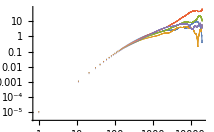
(* Mostramos lo que es seriesdeTAMSD   *)    ListLogLogPlot[seriesdeTAMSD[20000,10,"X"]]--→ -Graphics-

VLista[nombreParticula_, lag_, deltaDif_, eje]  da una lista con la velocidad  “eje” de la partícula  nombreParticula  evaluada mediante diferencias finita central con  Δ=deltaDif, evaluándose en las posiciones 1,1+lag,1+2lag,1+3lag, ....El valor de eje es “X” o “Y”

```mathematica
VLista[nombreParticula_,lag_,deltaDif_,eje_]:=Prepend[
Table[(PosicionLista[nombreParticula,eje][[n+deltaDif]]-PosicionLista[nombreParticula,eje][[n-deltaDif]])/(2*deltaDif*duracionFotograma),{n,lag+1,Length[datosdeParticula[nombreParticula]]-lag,lag}],(PosicionLista[nombreParticula,eje][[1+deltaDif]]-PosicionLista[nombreParticula,eje][[1]])/(deltaDif*duracionFotograma)];
```

Ejemplos

```mathematica
VLista[508, 2, 2, "X"]
```

{-1.25781,-1.14915,-1.17416,-1.36086}

```mathematica
VLista[508, 1, 1, "X"]
```

{-1.60654,-1.25781,-1.13682,-1.0405,-1.12477,-1.30782,-1.3849,-1.41389,-1.10535}

```mathematica
VLista[nombreParticula_,lag_,deltaDif_,eje_,{frameIni_,frameFin_}]:= If[frameFin<Length[datosdeParticula[nombreParticula]],
Table[(PosicionLista[nombreParticula,eje][[n+deltaDif]]-PosicionLista[nombreParticula,eje][[n-deltaDif]])/(2*deltaDif*duracionFotograma),{n,frameIni+lag,frameFin-lag,lag}] ,Table[(PosicionLista[nombreParticula,eje][[n+deltaDif]]-PosicionLista[nombreParticula,eje][[n-deltaDif]])/(2*deltaDif*duracionFotograma),{n,frameIni+lag,Length[datosdeParticula[nombreParticula]]-lag,lag}]]
```

```mathematica
serieTotaldeV[longitudMinimadelasSeries_,lag_,deltaDif_,eje_]:= serieTotaldeV[longitudMinimadelasSeries,lag,deltaDif,eje]=Module[{listaParticulasSeleccionadas},
listaParticulasSeleccionadas=listaParticulasconNumerodeDatosMayoroIgualque[longitudMinimadelasSeries];
Flatten[Table[VLista[listaParticulasSeleccionadas[[m,1]],lag,deltaDif,eje],{m,1,Length[listaParticulasSeleccionadas]}]]
]
```

CorrelationFunctionpaclet:ref/CorrelationFunction[{x_1,…,x_n},h] is equivalent to ∑_(i==1)^(n-h) (x_i-μ̂) (x_(i+h)-μ̂)/∑_(i=1)^n (x_i-μ̂)^2 with μ̂=Meanpaclet:ref/Mean[{x_1,…,x_n}].

Definimos la función de correlación de las velocidades en donde la lista de velocidades se calcula en tiempos separados por lag, en diferencias finitas con Δ=deltaDif,  y  donde el lag de la función de correlación (“lagDeCorrelacion”) se da en unidades de lagCalculoVelocidad.  Es decir,  en unidades de números de frame,  el lag de la función de correlación es igual a  
	lag*lagDeCorrelacion       (→ lag de correlación en frames)

```mathematica
autoCorrelacionV[particula_,lag_,deltaDif_,eje_,lagDeCorrelacion_]:= CorrelationFunction[VLista[particula,lag,deltaDif,eje],lagDeCorrelacion]
```

```mathematica
autoCorrelacionV[508,2,2,"X",2]
```

-0.444488

Con autoCorrelacionVLISTA   generamos una lista de autocorrelaciones de la velocidad  en la dirección eje  para varios valores de lag de correlación (en unidades de lagCalculoVelocidad), yendo este valor  de 0 a un valor máximo  (“lagDeCorrelacionFinal “) en incrementos iguales a   lagDeCorrelacionIncremento

```mathematica
autoCorrelacionVLISTA[particula_,lagCalculoVelocidad_,deltaDif_,eje_,{lagDeCorrelacionFinal_,lagDeCorrelacionIncremento_}]:=Table[{lagDeCorrelacion,autoCorrelacionV[particula,lagCalculoVelocidad,deltaDif,eje,lagDeCorrelacion]},{lagDeCorrelacion,0,lagDeCorrelacionFinal,lagDeCorrelacionIncremento}]
```

autoCorrelacionVLISTA[160, 2, 1, "X", {30, 2}]

{{0, 1.}, {2, 0.71968}, {4, 0.538127}, {6, 0.558843}, {8, 0.509515}, {10, 0.260868}, {12, 0.112798}, {14, 0.151133}, {16, 0.0676291}, {18, -0.196686}, {20, -0.218038}, {22, -0.206666}, {24, -0.267179}, {26, -0.375932}, {28, -0.336486}, {30, -0.275143}}

Con autoCorrelacionVLISTAFrames   generamos una lista de autocorrelaciones de la velocidad en dirección eje  para varios valores de lag de correlación (en unidades de frames), yendo este valor  de 0 a un valor máximo  (“lagDeCorrelacionFinal “) en incrementos iguales a   lagDeCorrelacionIncremento

```mathematica
autoCorrelacionVLISTAFrames[particula_,lagCalculoVelocidad_,deltaDif_,eje_,{lagDeCorrelacionFinal_,lagDeCorrelacionIncremento_}]:=Table[{lagDeCorrelacion*lagCalculoVelocidad,autoCorrelacionV[particula,lagCalculoVelocidad,deltaDif,eje,lagDeCorrelacion]},{lagDeCorrelacion,0,lagDeCorrelacionFinal,lagDeCorrelacionIncremento}]
```

autoCorrelacionVPromediada  proporciona una tabla con formato  
	{frame, autocorrelación velocidad y average sobre todas las series con longitud mínima mayor o igual que “longitudMinimadelasSeries”}.  
La autocorrelación se calcula para un lagCalculoVelocidad (en frames) dado .  Ojo:   lagDeCorrelacionFinal y lagDeCorrelacionIncremento  se dan en unidades de lagCalculoVelocidad.

```mathematica
autoCorrelacionVPromediada[longitudMinimadelasSeries_,lagCalculoVelocidad_,deltaDif_,eje_,{lagDeCorrelacionFinal_,lagDeCorrelacionIncremento_}]:= autoCorrelacionVPromediada[longitudMinimadelasSeries,lagCalculoVelocidad,deltaDif,eje,{lagDeCorrelacionFinal,lagDeCorrelacionIncremento}]=Module[{listaParticulasSeleccionadas},
listaParticulasSeleccionadas=listaParticulasconNumerodeDatosMayoroIgualque[longitudMinimadelasSeries];
Mean[Table[autoCorrelacionVLISTAFrames[listaParticulasSeleccionadas[[m,1]],lagCalculoVelocidad,deltaDif,eje,{lagDeCorrelacionFinal,lagDeCorrelacionIncremento}],{m,1,Length[listaParticulasSeleccionadas]}]]
]
```

```mathematica
etiquetaAvgV[longitudMinimadelasSeries_,lagCalculoVelocidad_,deltaDif_,eje_]:="Average (eje "<>eje<>" sobre series con long min="<>ToString[longitudMinimadelasSeries]<>"\n lag V="<>ToString[lagCalculoVelocidad]<>"con Δ="<>ToString[deltaDif]<>" . Unidades abcisa: frames";
```

# Posición

## Análisis del tamaño de los saltos Δx o Δy y coeficiente de difusión

#### Análisis del tamaño de los saltos Δx o Δy para deltan=10 y series con longitud mínima 20000

```mathematica
deltan=10;longituMin=20000;dataXCOMPLETA=serieTotaldeDeltaPosCOMPLETA[longituMin,deltan,"X"];dataYCOMPLETA=serieTotaldeDeltaPosCOMPLETA[longituMin,deltan,"Y"];{{Mean[dataXCOMPLETA],Variance[dataXCOMPLETA],Kurtosis[dataXCOMPLETA],Skewness[dataXCOMPLETA]},{Mean[dataYCOMPLETA],Variance[dataYCOMPLETA],Kurtosis[dataYCOMPLETA],Skewness[dataYCOMPLETA]}}//TableForm
```

-0.00130369 | 0.000851752 | 2.95161 | -0.092558
0.000180198 | 0.000897264 | 2.9306 | -0.0218374

```mathematica
deltan=10;longituMin=20000;dataX=serieTotaldeDeltaPos[longituMin,deltan,"X"];dataY=serieTotaldeDeltaPos[longituMin,deltan,"Y"];{{Mean[dataX],Variance[dataX],Kurtosis[dataX],Skewness[dataX]},{Mean[dataY],Variance[dataY],Kurtosis[dataY],Skewness[dataY]}}//TableForm
```

-0.00131038 | 0.000852012 | 2.95315 | -0.0903192
0.000177225 | 0.000898002 | 2.9295 | -0.0206965

```mathematica
{distX=EstimatedDistribution[dataX,NormalDistribution[m,s]],distY=EstimatedDistribution[dataY,NormalDistribution[m,s]]}
```

{NormalDistribution[-0.00131038,0.0291878],NormalDistribution[0.000177225,0.0299652]}

```mathematica
{distXCOMPLETA=EstimatedDistribution[dataXCOMPLETA,NormalDistribution[m,s]],distYCOMPLETA=EstimatedDistribution[dataYCOMPLETA,NormalDistribution[m,s]]}
```

{NormalDistribution[-0.00130369,0.0291847],NormalDistribution[0.000180198,0.0299542]}

```mathematica
{FindDistributionParameters[dataX,NormalDistribution[m,s]],FindDistributionParameters[dataY,NormalDistribution[m,s]]}
```

{{m→-0.00131038,s→0.0291878},{m→0.000177225,s→0.0299652}}

```mathematica
{FindDistributionParameters[dataXCOMPLETA,NormalDistribution[m,s]],FindDistributionParameters[dataYCOMPLETA,NormalDistribution[m,s]]}
```

{{m→-0.00130369,s→0.0291847},{m→0.000180198,s→0.0299542}}

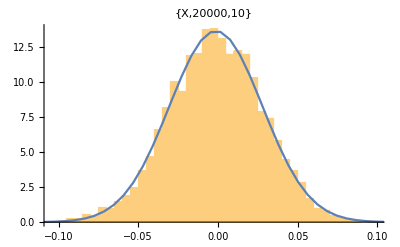

```mathematica
anchoCajas=0.005;k1=Show[Histogram[dataX,{anchoCajas},"ProbabilityDensity"],Plot[PDF[distX,y],{y,-10,10}],PlotLabel-> {"X",longituMin,deltan}]
```

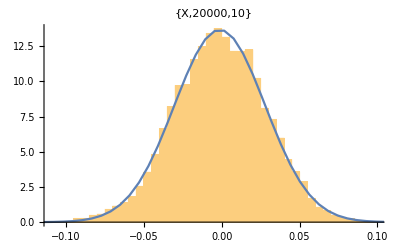

```mathematica
anchoCajas=0.005;k1=Show[Histogram[dataXCOMPLETA,{anchoCajas},"ProbabilityDensity"],Plot[PDF[distXCOMPLETA,y],{y,-10,10}],PlotLabel-> {"X",longituMin,deltan}]
```

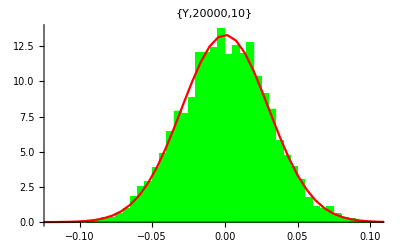

```mathematica
anchoCajas=0.005;k2=Show[Histogram[dataY,{anchoCajas},"ProbabilityDensity",ChartStyle->Green],Plot[PDF[distY,y],{y,-10,10},PlotStyle->Red],PlotLabel-> {"Y",longituMin,deltan}]
```

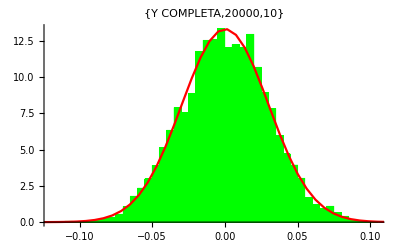

```mathematica
anchoCajas=0.005;k2=Show[Histogram[dataYCOMPLETA,{anchoCajas},"ProbabilityDensity",ChartStyle->Green],Plot[PDF[distYCOMPLETA,y],{y,-10,10},PlotStyle->Red],PlotLabel-> {"Y COMPLETA",longituMin,deltan}]
```

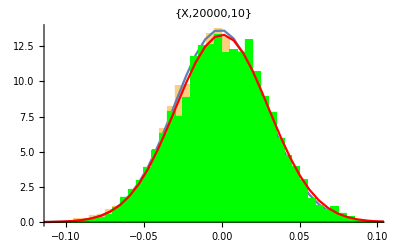

```mathematica
Show[k1,k2]
```

A small  p- value suggests that it is unlikely that the   data   came from    dist.

```mathematica
ℋX=DistributionFitTest[dataX,distX,"HypothesisTestData"];
```

```mathematica
ℋX["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 1.03351 | 0.340138
Baringhaus-Henze | 1.4728 | 0.0718248
Cramér-von Mises | 0.12047 | 0.493523
Jarque-Bera ALM | 14.4968 | 0.000987991
Kolmogorov-Smirnov | 0.0101142 | 0.257962
Kuiper | 0.0148944 | 0.176308
Mardia Combined | 14.4968 | 0.000987991
Mardia Kurtosis | -0.956376 | 0.338882
Mardia Skewness | 13.5959 | 0.000226678
Pearson χ^2 | 96.912 | 0.0835222
Watson U^2 | 0.090668 | 0.332232

```mathematica
ℋY=DistributionFitTest[dataY,distY,"HypothesisTestData"];
```

```mathematica
ℋYCOMPLETA=DistributionFitTest[dataYCOMPLETA,distYCOMPLETA,"HypothesisTestData"];
```

```mathematica
ℋY["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 1.20129 | 0.26704
Baringhaus-Henze | 2.67605 | 0.00291737
Cramér-von Mises | 0.193376 | 0.280678
Jarque-Bera ALM | 2.75332 | 0.256014
Kolmogorov-Smirnov | 0.0122482 | 0.0995254
Kuiper | 0.0211114 | 0.00409781
Mardia Combined | 2.75332 | 0.256014
Mardia Kurtosis | -1.43911 | 0.150121
Mardia Skewness | 0.71391 | 0.398149
Pearson χ^2 | 122.608 | 0.00121641
Watson U^2 | 0.187583 | 0.0493518

```mathematica
ℋYCOMPLETA["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 12.2333 | 1.3477×10^-6
Baringhaus-Henze | 31.6205 | 0.
Cramér-von Mises | 1.98892 | 0.0000135349
Jarque-Bera ALM | 27.9749 | 8.42009×10^-7
Mardia Combined | 27.9749 | 8.42009×10^-7
Mardia Kurtosis | -4.47904 | 7.49783×10^-6
Mardia Skewness | 7.94432 | 0.00482384
Pearson χ^2 | 1033.29 | 9.86102×10^-113

```mathematica
{DistributionFitTest[dataX,distX,Automatic],DistributionFitTest[dataY,distY,Automatic]}
```

{0.493523,0.280678}

```mathematica
{DistributionFitTest[dataXCOMPLETA,distXCOMPLETA,Automatic],DistributionFitTest[dataYCOMPLETA,distYCOMPLETA,Automatic]}
```

{0.000671427,0.0000135349}

#### Análisis de tamaño de saltos para deltan=10 y series con longitud mínima 19000

```mathematica
deltan=10;longituMin=19000;dataX=serieTotaldeDeltaPos[longituMin,deltan,"X"];dataY=serieTotaldeDeltaPos[longituMin,deltan,"Y"];{{Mean[dataX],Variance[dataX],Kurtosis[dataX],Skewness[dataX]},{Mean[dataY],Variance[dataY],Kurtosis[dataY],Skewness[dataY]}}//TableForm
```

-0.00160847 | 0.000825485 | 2.94595 | -0.0846655
0.000465866 | 0.000892484 | 3.00852 | -0.00754455

```mathematica
{distX=EstimatedDistribution[dataX,NormalDistribution[m,s]],distY=EstimatedDistribution[dataY,NormalDistribution[m,s]]}
```

{NormalDistribution[-0.00160847,0.0287301],NormalDistribution[0.000465866,0.0298732]}

```mathematica
{FindDistributionParameters[dataX,NormalDistribution[m,s]],FindDistributionParameters[dataY,NormalDistribution[m,s]]}
```

{{m→-0.00160847,s→0.0287301},{m→0.000465866,s→0.0298732}}

```mathematica
anchoCajas=0.005;k1=Show[Histogram[dataX,{anchoCajas},"ProbabilityDensity"],Plot[PDF[distX,y],{y,-10,10}],PlotLabel-> {"X",longituMin,deltan}];
```

```mathematica
anchoCajas=0.005;k2=Show[Histogram[dataY,{anchoCajas},"ProbabilityDensity",ChartStyle->Green],Plot[PDF[distY,y],{y,-10,10},PlotStyle->Red],PlotLabel-> {"Y",longituMin,deltan}];
```

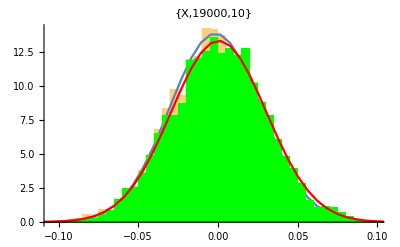

```mathematica
Show[k1,k2]
```

A small  p- value suggests that it is unlikely that the   data   came from    dist.

```mathematica
ℋX=DistributionFitTest[dataX,distX,"HypothesisTestData"];
```

```mathematica
ℋX["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 1.06693 | 0.323966
Baringhaus-Henze | 1.63711 | 0.0449079
Cramér-von Mises | 0.122102 | 0.486974
Jarque-Bera ALM | 15.761 | 0.000378035
Kolmogorov-Smirnov | 0.00843131 | 0.361683
Kuiper | 0.0135235 | 0.184362
Mardia Combined | 15.761 | 0.000378035
Mardia Kurtosis | -1.20798 | 0.227055
Mardia Skewness | 14.3198 | 0.000154237
Pearson χ^2 | 107.153 | 0.0525512
Watson U^2 | 0.0916575 | 0.325865

```mathematica
ℋY=DistributionFitTest[dataY,distY,"HypothesisTestData"];
```

```mathematica
ℋY["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 0.932743 | 0.394556
Baringhaus-Henze | 2.30104 | 0.00721791
Cramér-von Mises | 0.129243 | 0.459511
Jarque-Bera ALM | 0.154476 | 0.92567
Kolmogorov-Smirnov | 0.00794032 | 0.436466
Kuiper | 0.0157293 | 0.0540321
Mardia Combined | 0.154476 | 0.92567
Mardia Kurtosis | 0.190458 | 0.84895
Mardia Skewness | 0.113708 | 0.735962
Pearson χ^2 | 125.894 | 0.00264161
Watson U^2 | 0.127962 | 0.159926

```mathematica
{DistributionFitTest[dataX,distX,Automatic],DistributionFitTest[dataY,distY,Automatic]}
```

{0.486974,0.459511}

#### Análisis de tamaño de saltos para deltan=10 y series con longitud mínima 10000

```mathematica
deltan=10;longituMin=10000;dataX=serieTotaldeDeltaPos[longituMin,deltan,"X"];dataY=serieTotaldeDeltaPos[longituMin,deltan,"Y"];{{Mean[dataX],Variance[dataX],Kurtosis[dataX],Skewness[dataX]},{Mean[dataY],Variance[dataY],Kurtosis[dataY],Skewness[dataY]}}//TableForm
```

-0.00135693 | 0.000813396 | 3.07199 | -0.0737317
-0.00141362 | 0.000884083 | 3.08731 | 0.00755517

```mathematica
{distX=EstimatedDistribution[dataX,NormalDistribution[m,s]],distY=EstimatedDistribution[dataY,NormalDistribution[m,s]]}
```

{NormalDistribution[-0.00135693,0.0285198],NormalDistribution[-0.00141362,0.0297332]}

```mathematica
{FindDistributionParameters[dataX,NormalDistribution[m,s]],FindDistributionParameters[dataY,NormalDistribution[m,s]]}
```

{{m→-0.00135693,s→0.0285198},{m→-0.00141362,s→0.0297332}}

```mathematica
anchoCajas=0.005;k1=Show[Histogram[dataX,{anchoCajas},"ProbabilityDensity"],Plot[PDF[distX,y],{y,-10,10}],PlotLabel-> {"X",longituMin,deltan}];
```

```mathematica
anchoCajas=0.005;k2=Show[Histogram[dataY,{anchoCajas},"ProbabilityDensity",ChartStyle->Green],Plot[PDF[distY,y],{y,-10,10},PlotStyle->Red],PlotLabel-> {"Y",longituMin,deltan}];
```

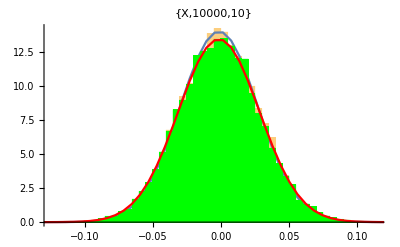

```mathematica
Show[k1,k2]
```

A small  p- value suggests that it is unlikely that the   data   came from    dist.

```mathematica
ℋX=DistributionFitTest[dataX,distX,"HypothesisTestData"];
```

```mathematica
ℋX["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 2.55272 | 0.0464918
Baringhaus-Henze | 3.89375 | 0.000049195
Cramér-von Mises | 0.304709 | 0.131112
Jarque-Bera ALM | 49.3399 | 1.93186×10^-11
Kolmogorov-Smirnov | 0.00585951 | 0.0978926
Kuiper | 0.00993505 | 0.00534065
Mardia Combined | 49.3399 | 1.93186×10^-11
Mardia Kurtosis | 3.08016 | 0.00206892
Mardia Skewness | 39.8078 | 2.80221×10^-10
Pearson χ^2 | 230.038 | 5.3378×10^-6
Watson U^2 | 0.236571 | 0.018757

```mathematica
ℋY=DistributionFitTest[dataY,distY,"HypothesisTestData"];
```

```mathematica
ℋY["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 1.38479 | 0.206546
Baringhaus-Henze | 2.55584 | 0.00216973
Cramér-von Mises | 0.161462 | 0.356465
Jarque-Bera ALM | 14.4212 | 0.000738711
Mardia Combined | 14.4212 | 0.000738711
Mardia Kurtosis | 3.7356 | 0.000187268
Mardia Skewness | 0.417973 | 0.51795
Pearson χ^2 | 207.599 | 0.000338452

```mathematica
{DistributionFitTest[dataX,distX,Automatic],DistributionFitTest[dataY,distY,Automatic]}
```

{0.131112,0.356465}

#### Coeficiente de difusión "microscópico" (o DifuSalto) D_x=Var[δx]/(2δt) o D_y=Var[δy]/(2δt)

```mathematica
headTable["X"]:=Style[#,{Red,Bold,15}]&/@{"δt", "D_x=Var[δx]/(2δt)", "media[δx]", "Var[δx]", "Curtosis", "Asimetría"};
```

```mathematica
headTable["Y"]:=Style[#,{Red,Bold,15}]&/@{"δt", "D_y=Var[δy]/(2δt)", "media[δy]", "Var[δy]", "Curtosis", "Asimetría"};
```

```mathematica
longituMin=20000;ejeV="X";(*deltan=Δt es la separación temporal correspondiente a Δx *)
kk=Table[{data=serieTotaldeDeltaPos[longituMin,deltan,ejeV];deltan,Variance[data]/(2*deltan),Mean[data],Variance[data],Kurtosis[data],Skewness[data]},{deltan,50,500,50}]
```

{{50,0.000201588,-0.00655191,0.0201588,2.95358,-0.093357},{100,0.000365087,-0.0131038,0.0730175,2.96606,-0.0813793},{150,0.000475085,-0.0192151,0.142525,3.12537,-0.115168},{200,0.000553296,-0.0262076,0.221318,3.1332,-0.135493},{250,0.000599643,-0.0327596,0.299822,3.17791,-0.0874136},{300,0.000619216,-0.0353949,0.371529,2.98129,-0.0350658},{350,0.000673418,-0.0448352,0.471393,2.93955,-0.184024},{400,0.000660546,-0.0524153,0.528437,3.19251,-0.126805},{450,0.000684685,-0.0530924,0.616216,3.05612,-0.0503652},{500,0.000698374,-0.0655191,0.698374,3.07739,-0.0915459}}

```mathematica
jj=Prepend[kk,headTable[ejeV]] // TableForm
```

δt | D_x=Var[δx]/(2δt) | media[δx] | Var[δx] | Curtosis | Asimetría
50 | 0.000201588 | -0.00655191 | 0.0201588 | 2.95358 | -0.093357
100 | 0.000365087 | -0.0131038 | 0.0730175 | 2.96606 | -0.0813793
150 | 0.000475085 | -0.0192151 | 0.142525 | 3.12537 | -0.115168
200 | 0.000553296 | -0.0262076 | 0.221318 | 3.1332 | -0.135493
250 | 0.000599643 | -0.0327596 | 0.299822 | 3.17791 | -0.0874136
300 | 0.000619216 | -0.0353949 | 0.371529 | 2.98129 | -0.0350658
350 | 0.000673418 | -0.0448352 | 0.471393 | 2.93955 | -0.184024
400 | 0.000660546 | -0.0524153 | 0.528437 | 3.19251 | -0.126805
450 | 0.000684685 | -0.0530924 | 0.616216 | 3.05612 | -0.0503652
500 | 0.000698374 | -0.0655191 | 0.698374 | 3.07739 | -0.0915459

```mathematica
longituMin=20000;ejeV="Y";(*deltan=Δt es la separación temporal correspondiente a Δy *)
kk=Table[{data=serieTotaldeDeltaPos[longituMin,deltan,ejeV];deltan,Variance[data]/(2*deltan),Mean[data],Variance[data],Kurtosis[data],Skewness[data]},{deltan,50,500,50}]
```

{{50,0.000212441,0.000886124,0.0212441,2.9219,-0.0301529},{100,0.000381736,0.00177225,0.0763472,2.88714,-0.0285966},{150,0.000498201,0.00258833,0.14946,3.074,-0.0615985},{200,0.000561353,0.00354449,0.224541,2.90791,0.0154047},{250,0.00058009,0.00443062,0.290045,2.84599,-0.0912793},{300,0.000603217,0.00284497,0.36193,3.00617,-0.143667},{350,0.000615466,0.00603943,0.430827,2.75673,0.0386549},{400,0.000616486,0.00708899,0.493189,3.0222,0.0778572},{450,0.000652751,0.00426745,0.587476,3.05327,0.0327607},{500,0.000632895,0.00886124,0.632895,2.94231,0.0796567}}

```mathematica
jj=Prepend[kk,headTable[ejeV]] // TableForm
```

δt | D_y=Var[δy]/(2δt) | media[δy] | Var[δy] | Curtosis | Asimetría
50 | 0.000212441 | 0.000886124 | 0.0212441 | 2.9219 | -0.0301529
100 | 0.000381736 | 0.00177225 | 0.0763472 | 2.88714 | -0.0285966
150 | 0.000498201 | 0.00258833 | 0.14946 | 3.074 | -0.0615985
200 | 0.000561353 | 0.00354449 | 0.224541 | 2.90791 | 0.0154047
250 | 0.00058009 | 0.00443062 | 0.290045 | 2.84599 | -0.0912793
300 | 0.000603217 | 0.00284497 | 0.36193 | 3.00617 | -0.143667
350 | 0.000615466 | 0.00603943 | 0.430827 | 2.75673 | 0.0386549
400 | 0.000616486 | 0.00708899 | 0.493189 | 3.0222 | 0.0778572
450 | 0.000652751 | 0.00426745 | 0.587476 | 3.05327 | 0.0327607
500 | 0.000632895 | 0.00886124 | 0.632895 | 2.94231 | 0.0796567

## TAMSD y coeficiente de difusión “macroscópico”

#### TAMSD para las series con un tamaño (o tiempo mínimo) mayor o igual que tiempoMinimoSerieDatosaComputar

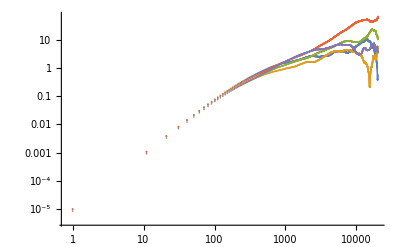

```mathematica
tiempoMinimoSerieDatosaComputar=20000;incrementoEntreVentanasTemporalesUsadas=10;ListLogLogPlot[seriesdeTAMSD[tiempoMinimoSerieDatosaComputar,incrementoEntreVentanasTemporalesUsadas,"X"]]
```

#### TAMSD PROMEDIADO sobre las series con un tamaño (o tiempo mínimo) mayor o igual que tiempoMinimoSerieDatosaComputar

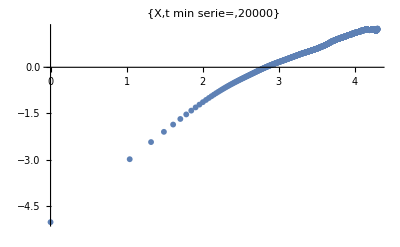

```mathematica
tiempoMinimoSerieDatosaComputar=20000;incrementoEntreVentanasTemporalesUsadas=10;ejeV="X";fa=ListPlot[Log[10,Mean[seriesdeTAMSD[tiempoMinimoSerieDatosaComputar,incrementoEntreVentanasTemporalesUsadas,ejeV]]],PlotRange->All,PlotMarkers->{Automatic,6},PlotLabel->{ejeV,"t min serie=",tiempoMinimoSerieDatosaComputar}]
```

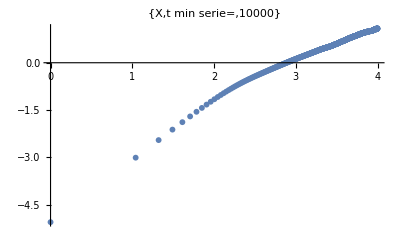

```mathematica
tiempoMinimoSerieDatosaComputar=10000;incrementoEntreVentanasTemporalesUsadas=10;ejeV="X";fa=ListPlot[Log[10,Mean[seriesdeTAMSD[tiempoMinimoSerieDatosaComputar,incrementoEntreVentanasTemporalesUsadas,ejeV]]],PlotRange->All,PlotMarkers->{Automatic,6},PlotLabel->{ejeV,"t min serie=",tiempoMinimoSerieDatosaComputar}]
```

#### TAMSD PROMEDIADO sobre las series con un tamaño (o tiempo mínimo) mayor o igual que tiempoMinimoSerieDatosaComputar y comparación con ajuste balístico (tiempos cortos) y difusivo (tiempos grandes).

```mathematica
fBalistico=Plot[-5.1+2 x,{x,0.01,2.5},PlotStyle->Blue];
```

```mathematica
fDifuNormal=Plot[-2.86+1 x,{x,2,4.4},PlotStyle->Red];
```

En la dirección X los resultados son una perita en dulce: todo sale como en nuestros mejores sueños.

Generando TAMSD de la serie... 57

Generando TAMSD de la serie... 56

Generando TAMSD de la serie... 50

Generando TAMSD de la serie... 7

Generando TAMSD de la serie... 2

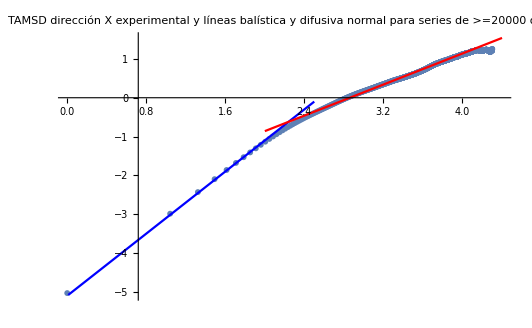

```mathematica
tiempoMinimoSerieDatosaComputar=20000;
incrementoEntreVentanasTemporalesUsadas=10;ejeV="X";fa=ListPlot[Log[10,Mean[seriesdeTAMSD[tiempoMinimoSerieDatosaComputar,incrementoEntreVentanasTemporalesUsadas,ejeV]]],PlotRange->{{0.7,4.5},All},PlotMarkers->{Automatic,6},PlotLabel->{ejeV,"t min serie=",tiempoMinimoSerieDatosaComputar}];Show[fa,fBalistico,fDifuNormal,PlotStyle->{Black,Red,Blue},PlotRange->{All,All},PlotLabel->"TAMSD dirección "<>ejeV<>" experimental y líneas balística y difusiva normal para series de >="<>ToString[tiempoMinimoSerieDatosaComputar]<>" datos"]
```

Generando TAMSD de la serie... 57

Generando TAMSD de la serie... 56

Generando TAMSD de la serie... 50

Generando TAMSD de la serie... 7

Generando TAMSD de la serie... 2

Generando TAMSD de la serie... 52

Generando TAMSD de la serie... 130

Generando TAMSD de la serie... 125

Generando TAMSD de la serie... 113

Generando TAMSD de la serie... 122

Generando TAMSD de la serie... 164

Generando TAMSD de la serie... 197

Generando TAMSD de la serie... 8

Generando TAMSD de la serie... 163

Generando TAMSD de la serie... 214

Generando TAMSD de la serie... 211

Generando TAMSD de la serie... 60

Generando TAMSD de la serie... 41

Generando TAMSD de la serie... 230

Generando TAMSD de la serie... 236

Generando TAMSD de la serie... 203

Generando TAMSD de la serie... 28

Generando TAMSD de la serie... 243

Generando TAMSD de la serie... 247

Generando TAMSD de la serie... 252

Generando TAMSD de la serie... 48

Generando TAMSD de la serie... 225

Generando TAMSD de la serie... 246

Generando TAMSD de la serie... 256

Generando TAMSD de la serie... 30

Generando TAMSD de la serie... 46

Generando TAMSD de la serie... 111

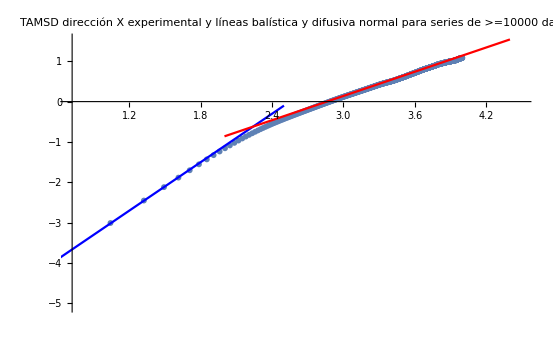

```mathematica
tiempoMinimoSerieDatosaComputar=10000;
incrementoEntreVentanasTemporalesUsadas=10;ejeV="X";fa=ListPlot[Log[10,Mean[seriesdeTAMSD[tiempoMinimoSerieDatosaComputar,incrementoEntreVentanasTemporalesUsadas,ejeV]]],PlotRange->{{0.7,4.5},All},PlotMarkers->{Automatic,6},PlotLabel->{ejeV,"t min serie=",tiempoMinimoSerieDatosaComputar}];Show[fa,fBalistico,fDifuNormal,PlotStyle->{Black,Red,Blue},PlotRange->{{0.7,4.5},All},PlotLabel->"TAMSD dirección "<>ejeV<>" experimental y líneas balística y difusiva normal para series de >="<>ToString[tiempoMinimoSerieDatosaComputar]<>" datos"]
```

En la dirección Y los resultados son malos especialmente en lo que se refiere a la parte difusiva.

Generando TAMSD de la serie... 57

Generando TAMSD de la serie... 56

Generando TAMSD de la serie... 50

Generando TAMSD de la serie... 7

Generando TAMSD de la serie... 2

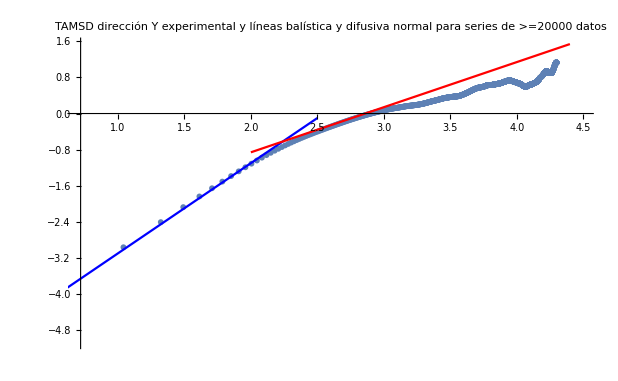

```mathematica
tiempoMinimoSerieDatosaComputar=20000;
incrementoEntreVentanasTemporalesUsadas=10;ejeV="Y";fa=ListPlot[Log[10,Mean[seriesdeTAMSD[tiempoMinimoSerieDatosaComputar,incrementoEntreVentanasTemporalesUsadas,ejeV]]],PlotRange->{{0.7,4.5},All},PlotMarkers->{Automatic,6},PlotLabel->{ejeV,"t min serie=",tiempoMinimoSerieDatosaComputar}];Show[fa,fBalistico,fDifuNormal,PlotStyle->{Black,Red,Blue},PlotRange->{{0.7,4.5},All},PlotLabel->"TAMSD dirección "<>ejeV<>" experimental y líneas balística y difusiva normal para series de >="<>ToString[tiempoMinimoSerieDatosaComputar]<>" datos"]
```

Generando TAMSD de la serie... 57

Generando TAMSD de la serie... 56

Generando TAMSD de la serie... 50

Generando TAMSD de la serie... 7

Generando TAMSD de la serie... 2

Generando TAMSD de la serie... 52

Generando TAMSD de la serie... 130

Generando TAMSD de la serie... 125

Generando TAMSD de la serie... 113

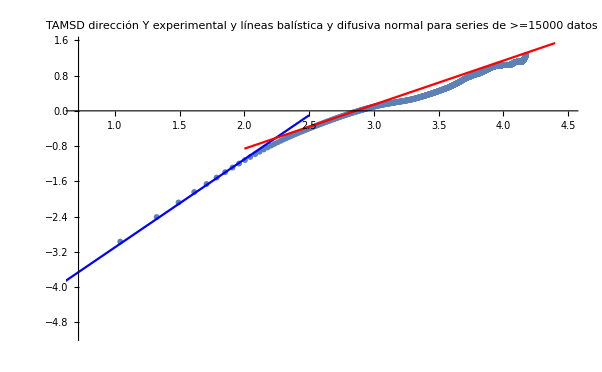

```mathematica
tiempoMinimoSerieDatosaComputar=15000;
incrementoEntreVentanasTemporalesUsadas=10;ejeV="Y";fa=ListPlot[Log[10,Mean[seriesdeTAMSD[tiempoMinimoSerieDatosaComputar,incrementoEntreVentanasTemporalesUsadas,ejeV]]],PlotRange->{{0.7,4.5},All},PlotMarkers->{Automatic,6},PlotLabel->{ejeV,"t min serie=",tiempoMinimoSerieDatosaComputar}];Show[fa,fBalistico,fDifuNormal,PlotStyle->{Black,Red,Blue},PlotRange->{{0.7,4.5},All},PlotLabel->"TAMSD dirección "<>ejeV<>" experimental y líneas balística y difusiva normal para series de >="<>ToString[tiempoMinimoSerieDatosaComputar]<>" datos"]
```

Generando TAMSD de la serie... 57

Generando TAMSD de la serie... 56

Generando TAMSD de la serie... 50

Generando TAMSD de la serie... 7

Generando TAMSD de la serie... 2

Generando TAMSD de la serie... 52

Generando TAMSD de la serie... 130

Generando TAMSD de la serie... 125

Generando TAMSD de la serie... 113

Generando TAMSD de la serie... 122

Generando TAMSD de la serie... 164

Generando TAMSD de la serie... 197

Generando TAMSD de la serie... 8

Generando TAMSD de la serie... 163

Generando TAMSD de la serie... 214

Generando TAMSD de la serie... 211

Generando TAMSD de la serie... 60

Generando TAMSD de la serie... 41

Generando TAMSD de la serie... 230

Generando TAMSD de la serie... 236

Generando TAMSD de la serie... 203

Generando TAMSD de la serie... 28

Generando TAMSD de la serie... 243

Generando TAMSD de la serie... 247

Generando TAMSD de la serie... 252

Generando TAMSD de la serie... 48

Generando TAMSD de la serie... 225

Generando TAMSD de la serie... 246

Generando TAMSD de la serie... 256

Generando TAMSD de la serie... 30

Generando TAMSD de la serie... 46

Generando TAMSD de la serie... 111

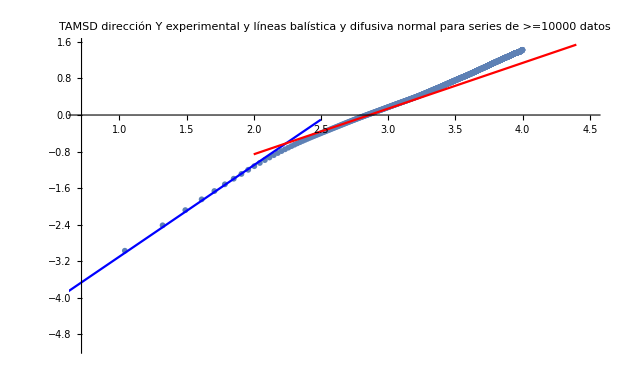

```mathematica
tiempoMinimoSerieDatosaComputar=10000;
incrementoEntreVentanasTemporalesUsadas=10;ejeV="Y";fa=ListPlot[Log[10,Mean[seriesdeTAMSD[tiempoMinimoSerieDatosaComputar,incrementoEntreVentanasTemporalesUsadas,ejeV]]],PlotRange->{{0.7,4.5},All},PlotMarkers->{Automatic,6},PlotLabel->{ejeV,"t min serie=",tiempoMinimoSerieDatosaComputar}];Show[fa,fBalistico,fDifuNormal,PlotStyle->{Black,Red,Blue},PlotRange->{{0.7,4.5},All},PlotLabel->"TAMSD dirección "<>ejeV<>" experimental y líneas balística y difusiva normal para series de >="<>ToString[tiempoMinimoSerieDatosaComputar]<>" datos"]
```

Ajustes del valor promedio de las TAMSD   para tiempos cortos....

```mathematica
Fit[Log[10,Take[Mean[seriesdeTAMSD[20000,10,#]],{1,10}]],{1,z},z]& /@{"X","Y"} //TableForm
```

-5.02265+1.95423 z
-4.9868+1.94581 z

El coeficiente z del ajuste esta en acuerdo razonable con la predicción teórica, que es 2 (comportamiento balísitico)

Para  tiempos largos....

```mathematica
Fit[Log[10,Take[Mean[seriesdeTAMSD[10000,10,#]],{20,900}]],{1,z},z]& /@{"X","Y"}//TableForm
```

-2.91648+1.00716 z
-3.52449+1.23001 z

El coeficiente de z del ajuste primero (eje X) es bueno :-)  (similar al resultado teórico 1), mientras que el segundo   (eje Y), es muy deficiente  :-(

## Trayectorias x(t) o y(t) de varias partículas

#### walk1DY[nombreParticula_, deltan_] es una lista con las posiciones y de las partículas cada deltan frames walk1DY[nombreParticula_,deltan_,{pasoIni_,pasoFin_}] es una lista con las posiciones y de las partículas cada deltan frames como si la partícula hubiera empezado a andar en el pasoIni y terminar en el pasoFin (pasos en unidades de deltan) caminata2D[nombreParticula_,deltan_] dibuja la trayectoria de la partícula nombreParticula en el plano 2D

```mathematica
walk1D[nombreParticula_,deltan_,eje_]:=FoldList[Plus,0,DeltaPosicionLista[nombreParticula,deltan,eje]]
```

```mathematica
walk1D[nombreParticula_,deltan_,eje_,{pasoIni_,pasoFin_}]:=FoldList[Plus,0,Take[DeltaPosicionLista[nombreParticula,deltan,eje],{pasoIni,pasoFin}]]
```

```mathematica
caminata2D[nombreParticula_,deltan_]:=ListPlot[Thread[{walk1D[nombreParticula,deltan,"X"],walk1D[nombreParticula,deltan,"Y"]}],PlotLabel->StringJoin["Caminata  2D (x,y)  de partícula ",ToString[nombreParticula]," con pasos de tamaño ", ToString[deltan]]]
```

```mathematica
nombreParticula=508;walk1D[nombreParticula,1,"X"]
```

{0,-0.00401635,-0.00628903,-0.00970043,-0.0114915,-0.0153243,-0.0180307,-0.0222488,-0.0251001,-0.0277756}

```mathematica
nombreParticula=508;walk1D[nombreParticula,1,"Y"]
```

{0,0.00553049,0.0166685,0.0230718,0.0327818,0.0386737,0.0493235,0.0560045,0.0662311,0.0723233}

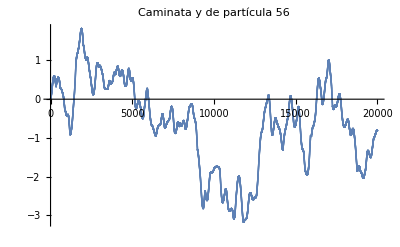

```mathematica
nombreParticula=56;ListPlot[walk1D[nombreParticula,1,"Y"],PlotLabel->StringJoin["Caminata y de partícula ",ToString[nombreParticula]]]
```

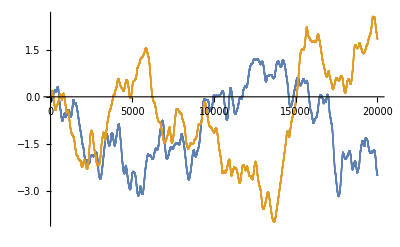

```mathematica
ejeV="X";ListPlot[{walk1D[56,1,ejeV],walk1D[2,1,ejeV]}]
```

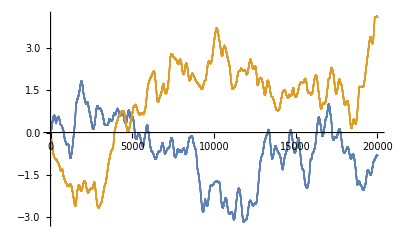

```mathematica
ejeV="Y";ListPlot[{walk1D[56,1,ejeV],walk1D[2,1,ejeV]}]
```

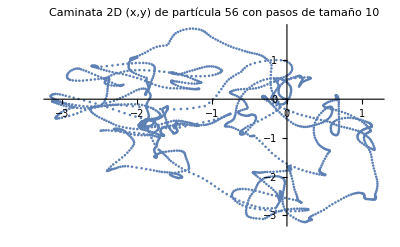

```mathematica
caminata2D[56,10]
```

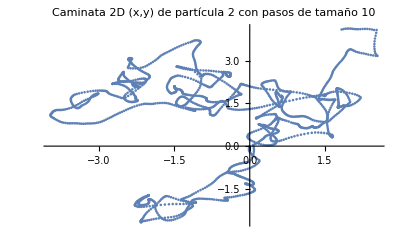

```mathematica
caminata2D[2,10]
```

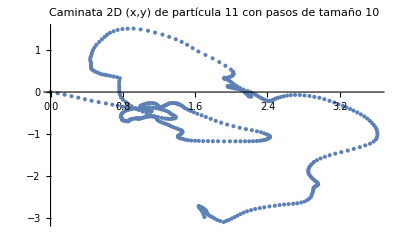

```mathematica
caminata2D[11,10]
```

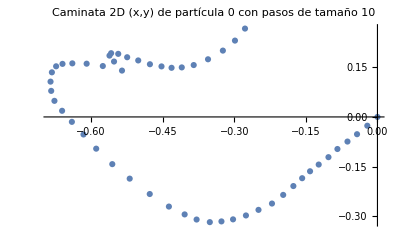

```mathematica
caminata2D[0,10]
```

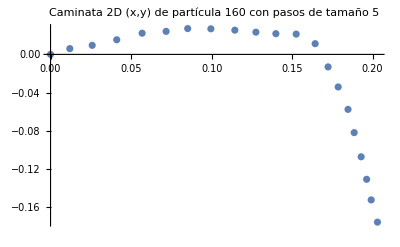

```mathematica
caminata2D[160,5]
```

# Velocidad

## Velocidad en la dirección y en unidades de diámetros de ppp por segundo. Se usa fórmula diferencias central de dos puntos con distancia derecha-izquierda igual a +- lag

Ejemplos

```mathematica
nombreParticula=505;separacionTemporal=2;deltaDif=1;ejeV="X"; VLista[nombreParticula,separacionTemporal,deltaDif,ejeV]
```

{0.835618,0.863432,0.59742,1.52699,0.914652,1.01719,1.42424,1.26085,-1.45047,-0.649699,-0.867041,-0.620655,-0.421581,-0.455914,-0.462283,-0.439052,-0.684437,-0.332018,-0.37913,-0.142717,-0.358327,-0.319829,-0.148107,-0.200073,-0.0522342,-0.142853,0.133153,-0.170413,0.135492,-0.0274498,-0.183185,0.195234}

```mathematica
nombreParticula=505;separacionTemporal=2;deltaDif=1;ejeV="X";frameInicial=1;frameFinal=16; VLista[nombreParticula,separacionTemporal,deltaDif,ejeV,{frameInicial,frameFinal}]
```

{0.863432,0.59742,1.52699,0.914652,1.01719,1.42424}

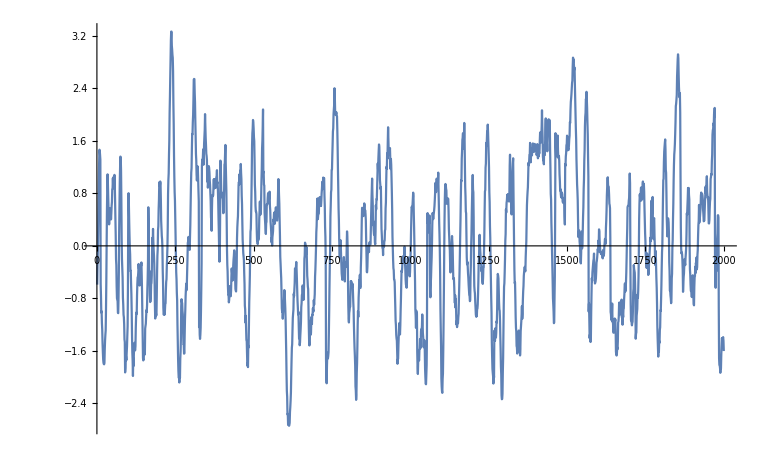

```mathematica
nombreParticula=2;separacionTemporal=10;deltaDif=5;ejeV="X"; ListPlot[VLista[nombreParticula,separacionTemporal,deltaDif,ejeV],Joined->True]
```

#### En las figuras siguientes se muestra la velocidad frente al tiempo y se observa: 1) que la velocidad no es constante con cambios bruscos, lo que se esperaría si las partículas se comportaran como ppp que se mueven libremente entre choques 2) Las velocidades cambian de frame a frame, lo que indica que hay aceleraciones. 3) las velocidades cambian de una forma relativamente lineal entre intervalos que se separan por cambios bruscos de la velocidad. 3a) Hipótesis a: Los cambios bruscos pueden deberse *principalmente* a choques entre las ppp 3b) Hipótesis b: Los cambios bruscos pueden deberse a choques entre las ppp *y* fuerzas hidrodinámicas turbulentas. 3b) Entre los choques (o cambios bruscos turbulentos) la aceleración es relativamente constante y por eso la velocidad en escalas de (grosso modo) unos 100 frames=0.25s cambia linealmente.

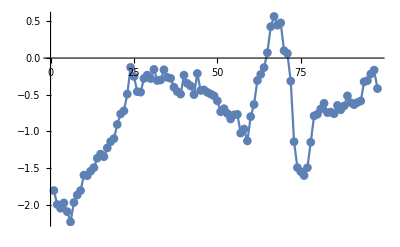

```mathematica
nombreParticula=2;separacionTemporal=10;deltaDif=5;ejeV="Y";{frameInicial=1,frameFinal=1000};ListPlot[VLista[nombreParticula,separacionTemporal,deltaDif,ejeV,{frameInicial,frameFinal}],Joined->True,PlotMarkers->{Automatic}]
```

#### Mostramos el efecto que tiene el lag (1, 5, 10, 20) en la estimación no ruidosa de la velocidad (la estimación ruidosa se debe probablemente a falta de precisión en la posición de la partícula). Se ve que con lag=10 los resultados son razonables

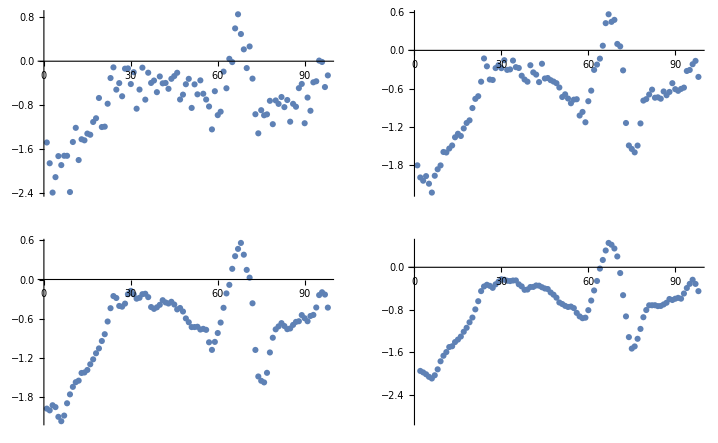

```mathematica
nombreParticula=2;separacionTemporal=10;deltaDif=5;ejeV="Y";{frameInicial=1,frameFinal=1000};GraphicsGrid[{{ListPlot[VLista[nombreParticula,separacionTemporal,1,ejeV,{frameInicial,frameFinal}]],ListPlot[VLista[nombreParticula,separacionTemporal,5,ejeV,{frameInicial,frameFinal}]]},{ListPlot[VLista[nombreParticula,separacionTemporal,10,ejeV,{frameInicial,frameFinal}]],ListPlot[VLista[nombreParticula,separacionTemporal,20,ejeV,{frameInicial,frameFinal}]]}}]
```

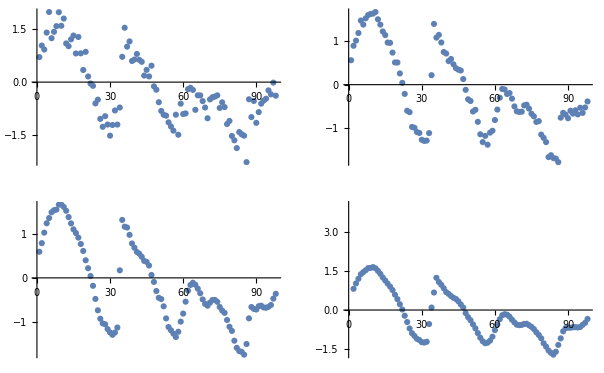

```mathematica
nombreParticula=56;separacionTemporal=10;deltaDif=5;ejeV="Y";{frameInicial=1,frameFinal=1000};GraphicsGrid[{{ListPlot[VLista[nombreParticula,separacionTemporal,1,ejeV,{frameInicial,frameFinal}]],ListPlot[VLista[nombreParticula,separacionTemporal,5,ejeV,{frameInicial,frameFinal}]]},{ListPlot[VLista[nombreParticula,separacionTemporal,10,ejeV,{frameInicial,frameFinal}]],ListPlot[VLista[nombreParticula,separacionTemporal,20,ejeV,{frameInicial,frameFinal}]]}}]
```

#### Calculo de la varianza de la componente x o y de la velocidad. Depende notablemente del valor del lag usado en su cálculo.

```mathematica
nombreParticula=2;separacionTemporal=10;deltaDif=5;ejeV="Y";Variance[VLista[nombreParticula,separacionTemporal,deltaDif,ejeV]]
```

1.26221

```mathematica
nombreParticula=2;deltaDif=5;ejeV="X";
Table[{separacionTemporal,Variance[VLista[nombreParticula,separacionTemporal,deltaDif,ejeV]]},{separacionTemporal,5,10,1}]
```

{{5,1.20442},{6,1.20149},{7,1.2053},{8,1.20174},{9,1.20482},{10,1.2048}}

```mathematica
nombreParticula=2;deltaDif=5;ejeV="Y";
Table[{separacionTemporal,Variance[VLista[nombreParticula,separacionTemporal,deltaDif,ejeV]]},{separacionTemporal,5,10,1}]
```

{{5,1.2627},{6,1.26571},{7,1.26283},{8,1.26462},{9,1.2632},{10,1.26221}}

```mathematica
nombreParticula=2;ejeV="X";separacionTemporal=20;
Table[{deltaDif,Variance[VLista[nombreParticula,separacionTemporal,deltaDif,ejeV]]},{deltaDif,1,10,1}]
```

{{1,1.25944},{2,1.20573},{3,1.21952},{4,1.21311},{5,1.20958},{6,1.20679},{7,1.20293},{8,1.19974},{9,1.19703},{10,1.19332}}

```mathematica
nombreParticula=2;ejeV="Y";separacionTemporal=20;
Table[{deltaDif,Variance[VLista[nombreParticula,separacionTemporal,deltaDif,ejeV]]},{deltaDif,1,10,1}]
```

{{1,1.35393},{2,1.2817},{3,1.28901},{4,1.27928},{5,1.26603},{6,1.26627},{7,1.26719},{8,1.26313},{9,1.26266},{10,1.25594}}

#### Histograma de velocidades de partículas individuales

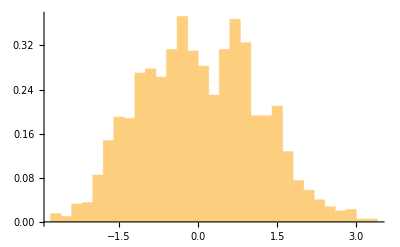

```mathematica
nombreParticula=2;separacionTemporal=10;deltaDif=5;ejeV="X";Histogram[VLista[nombreParticula,separacionTemporal,deltaDif,ejeV],{0.2},"PDF"]
```

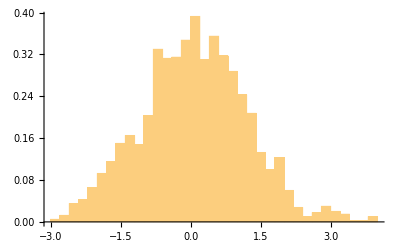

```mathematica
nombreParticula=2;separacionTemporal=10;deltaDif=5;ejeV="Y";Histogram[VLista[nombreParticula,separacionTemporal,deltaDif,ejeV],{0.2},"PDF"]
```

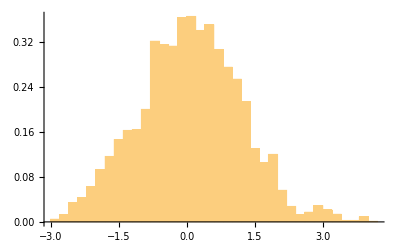

```mathematica
nombreParticula=2;separacionTemporal=5;deltaDif=5;ejeV="Y";Histogram[VLista[nombreParticula,separacionTemporal,deltaDif,ejeV],{0.2},"PDF"]
```

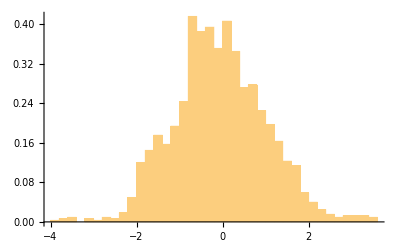

```mathematica
nombreParticula=130;separacionTemporal=10;deltaDif=5;ejeV="X";Histogram[VLista[nombreParticula,separacionTemporal,deltaDif,ejeV],{0.2},"PDF"]
```

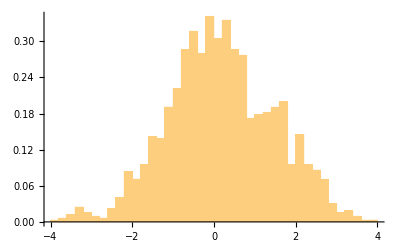

```mathematica
nombreParticula=130;separacionTemporal=10;deltaDif=5;ejeV="Y";Histogram[VLista[nombreParticula,separacionTemporal,deltaDif,ejeV],{0.2},"PDF"]
```

#### Histograma (UNIFICADO) de velocidades de partículas con serie de datos con una longitud mínima

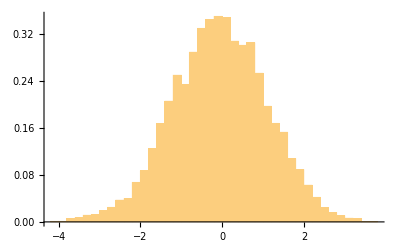

```mathematica
longMinimaSeriesdeDatos=19000;separacionTemporal=10;deltaDif=10;ejeV="X";Histogram[serieTotaldeV[longMinimaSeriesdeDatos,separacionTemporal,deltaDif,ejeV],{0.2},"PDF"]
```

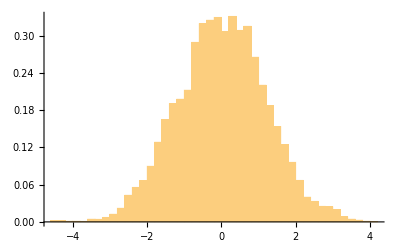

```mathematica
longMinimaSeriesdeDatos=19000;separacionTemporal=10;deltaDif=10;ejeV="Y";Histogram[serieTotaldeV[longMinimaSeriesdeDatos,separacionTemporal,deltaDif,ejeV],{0.2},"PDF"]
```

#### Histograma (UNIFICADO) de velocidades de partículas con serie de datos con una longitud mínima

### Histograma (UNIFICADO) y ANÁLISIS de velocidades de partículas con serie de datos con una longitud mínima

#### Longitud mínima 20000, lag=10,deltaDif=10, eje X

```mathematica
longMinimaSeriesdeDatos=20000;separacionTemporal=10;deltaDif=10;ejeV="X"; 
data=serieTotaldeV[longMinimaSeriesdeDatos,separacionTemporal,deltaDif,ejeV];{Mean[data],Variance[data],Kurtosis[data],Skewness[data]}
```

{-0.0525813,1.34835,2.95573,-0.092317}

```mathematica
dist=EstimatedDistribution[data,NormalDistribution[m,s]]
```

NormalDistribution[-0.0525813,1.16113]

```mathematica
FindDistributionParameters[data,NormalDistribution[m,s]]
```

{m→-0.0525813,s→1.16113}

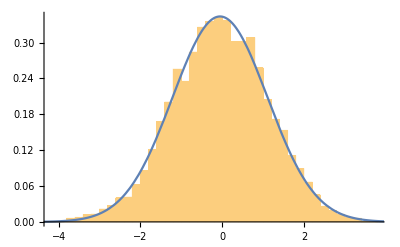

```mathematica
anchoCajas=0.2;Show[Histogram[data,{anchoCajas},"ProbabilityDensity"],Plot[PDF[dist,y],{y,-10,10}]]
```

A small  p- value suggests that it is unlikely that the   data   came from    dist.

```mathematica
ℋ=DistributionFitTest[data,dist,"HypothesisTestData"];
```

```mathematica
ℋ["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 1.04799 | 0.333026
Baringhaus-Henze | 1.51085 | 0.0645534
Cramér-von Mises | 0.120672 | 0.492703
Jarque-Bera ALM | 15.0084 | 0.000833605
Kolmogorov-Smirnov | 0.0101782 | 0.251387
Kuiper | 0.0155266 | 0.131144
Mardia Combined | 15.0084 | 0.000833605
Mardia Kurtosis | -0.903695 | 0.366157
Mardia Skewness | 14.204 | 0.000164018
Pearson χ^2 | 107.6 | 0.0179147
Watson U^2 | 0.0894006 | 0.340502

```mathematica
ℋ=DistributionFitTest[data,dist,Automatic]
```

0.492703

#### Longitud mínima 20000, lag=10,deltaDif=10, eje Y

```mathematica
longMinimaSeriesdeDatos=20000;separacionTemporal=10;deltaDif=10;ejeV="Y"; 
data=serieTotaldeV[longMinimaSeriesdeDatos,separacionTemporal,deltaDif,ejeV];{Mean[data],Variance[data],Kurtosis[data],Skewness[data]}
```

{0.00704233,1.42128,2.92916,-0.0224109}

```mathematica
dist=EstimatedDistribution[data,NormalDistribution[m,s]]
```

NormalDistribution[0.00704233,1.19211]

```mathematica
FindDistributionParameters[data,NormalDistribution[m,s]]
```

{m→0.00704233,s→1.19211}

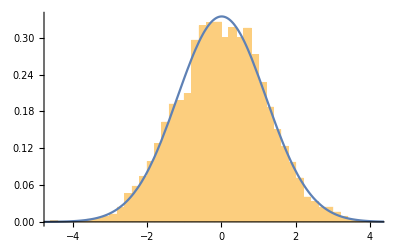

```mathematica
anchoCajas=0.2;Show[Histogram[data,{anchoCajas},"ProbabilityDensity"],Plot[PDF[dist,y],{y,-10,10}]]
```

A small  p- value suggests that it is unlikely that the   data   came from    dist.

```mathematica
ℋ=DistributionFitTest[data,dist,"HypothesisTestData"];
```

```mathematica
ℋ["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 1.18609 | 0.272883
Baringhaus-Henze | 2.683 | 0.00286755
Cramér-von Mises | 0.189128 | 0.28956
Jarque-Bera ALM | 2.89624 | 0.238322
Kolmogorov-Smirnov | 0.0108248 | 0.191807
Kuiper | 0.0185928 | 0.0235009
Mardia Combined | 2.89624 | 0.238322
Mardia Kurtosis | -1.44597 | 0.148185
Mardia Skewness | 0.837083 | 0.360232
Pearson χ^2 | 112.096 | 0.00850129
Watson U^2 | 0.182608 | 0.0544819

```mathematica
ℋ=DistributionFitTest[data,dist,Automatic]
```

0.28956

#### Longitud mínima 20000, lag=10,deltaDif=5, eje X

```mathematica
longMinimaSeriesdeDatos=20000;separacionTemporal=10;deltaDif=5;ejeV="X"; 
data=serieTotaldeV[longMinimaSeriesdeDatos,separacionTemporal,deltaDif,ejeV];{Mean[data],Variance[data],Kurtosis[data],Skewness[data]}
```

{-0.0526011,1.36329,2.95094,-0.0942023}

```mathematica
dist=EstimatedDistribution[data,NormalDistribution[m,s]]
```

NormalDistribution[-0.0526011,1.16754]

```mathematica
FindDistributionParameters[data,NormalDistribution[m,s]]
```

{m→-0.0526011,s→1.16754}

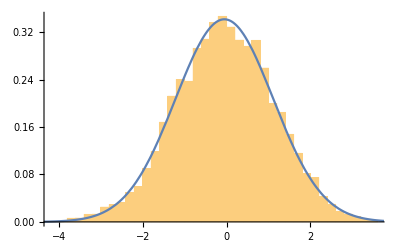

```mathematica
anchoCajas=0.2;Show[Histogram[data,{anchoCajas},"ProbabilityDensity"],Plot[PDF[dist,y],{y,-10,10}]]
```

A small  p- value suggests that it is unlikely that the   data   came from    dist.

```mathematica
ℋ=DistributionFitTest[data,dist,"HypothesisTestData"];
```

```mathematica
ℋ["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 1.10231 | 0.307764
Baringhaus-Henze | 1.57791 | 0.0535053
Cramér-von Mises | 0.131083 | 0.452732
Jarque-Bera ALM | 15.7789 | 0.000601111
Kolmogorov-Smirnov | 0.0101858 | 0.250611
Kuiper | 0.0148084 | 0.183259
Mardia Combined | 15.7789 | 0.000601111
Mardia Kurtosis | -1.00141 | 0.316626
Mardia Skewness | 14.7901 | 0.000120163
Pearson χ^2 | 107.088 | 0.0194335
Watson U^2 | 0.0975541 | 0.29052

```mathematica
ℋ=DistributionFitTest[data,dist,Automatic]
```

0.452732

#### Longitud mínima 20000, lag=10,deltaDif=5, eje Y

#### Longitud mínima 10000, lag=10,deltaDif=10, eje X

```mathematica
longMinimaSeriesdeDatos=10000;separacionTemporal=10;deltaDif=10;ejeV="X"; 
data=serieTotaldeV[longMinimaSeriesdeDatos,separacionTemporal,deltaDif,ejeV];{Mean[data],Variance[data],Kurtosis[data],Skewness[data]}
```

{-0.0543581,1.28616,3.07289,-0.0734238}

```mathematica
dist=EstimatedDistribution[data,NormalDistribution[m,s]]
```

NormalDistribution[-0.0543581,1.13408]

```mathematica
FindDistributionParameters[data,NormalDistribution[m,s]]
```

{m→-0.0543581,s→1.13408}

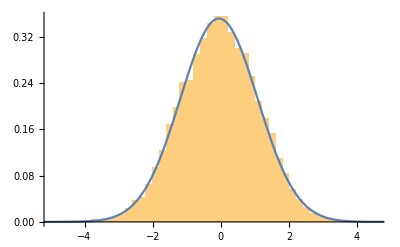

```mathematica
anchoCajas=0.2;Show[Histogram[data,{anchoCajas},"ProbabilityDensity"],Plot[PDF[dist,y],{y,-10,10}]]
```

A small  p- value suggests that it is unlikely that the   data   came from    dist.

```mathematica
ℋ=DistributionFitTest[data,dist,"HypothesisTestData"];
```

```mathematica
ℋ["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 2.51932 | 0.0483996
Baringhaus-Henze | 3.88446 | 0.0000504088
Cramér-von Mises | 0.297623 | 0.137274
Jarque-Bera ALM | 49.2472 | 2.02347×10^-11
Mardia Combined | 49.2472 | 2.02347×10^-11
Mardia Kurtosis | 3.11866 | 0.00181676
Mardia Skewness | 39.476 | 3.32116×10^-10
Pearson χ^2 | 218.723 | 0.000047127

```mathematica
ℋ=DistributionFitTest[data,dist,Automatic]
```

0.137274

#### Longitud mínima 10000, lag=10,deltaDif=10, eje Y

```mathematica
longMinimaSeriesdeDatos=10000;separacionTemporal=10;deltaDif=10;ejeV="Y"; 
data=serieTotaldeV[longMinimaSeriesdeDatos,separacionTemporal,deltaDif,ejeV];{Mean[data],Variance[data],Kurtosis[data],Skewness[data]}
```

{-0.056302,1.39823,3.0897,0.00674339}

```mathematica
dist=EstimatedDistribution[data,NormalDistribution[m,s]]
```

NormalDistribution[-0.056302,1.18246]

```mathematica
FindDistributionParameters[data,NormalDistribution[m,s]]
```

{m→-0.056302,s→1.18246}

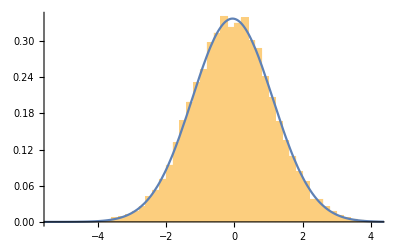

```mathematica
anchoCajas=0.2;Show[Histogram[data,{anchoCajas},"ProbabilityDensity"],Plot[PDF[dist,y],{y,-10,10}]]
```

A small  p- value suggests that it is unlikely that the   data   came from    dist.

```mathematica
ℋ=DistributionFitTest[data,dist,"HypothesisTestData"];
```

```mathematica
ℋ["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 1.32117 | 0.225583
Baringhaus-Henze | 2.08466 | 0.00943907
Cramér-von Mises | 0.149574 | 0.390875
Jarque-Bera ALM | 15.1126 | 0.000522818
Mardia Combined | 15.1126 | 0.000522818
Mardia Kurtosis | 3.83792 | 0.000124083
Mardia Skewness | 0.332979 | 0.56391
Pearson χ^2 | 191.592 | 0.00416211

```mathematica
ℋ=DistributionFitTest[data,dist,Automatic]
```

0.390875

## Autocorrelación de velocidades La autocorrelación se reduce en un factor 1/e después de unos 100 frames, i.e., 1/4 segundos, aproximadamente. Tras 20*10 frames=1/2 segundo cae hasta casi cero y se mantiene después “oscilando-fluctuando” en torno a cero.

CorrelationFunctionpaclet:ref/CorrelationFunction[{x_1,…,x_n},h] is equivalent to ∑_(i==1)^(n-h) (x_i-μ̂) (x_(i+h)-μ̂)/∑_(i=1)^n (x_i-μ̂)^2 with μ̂=Meanpaclet:ref/Mean[{x_1,…,x_n}].

#### Autocorrelación de velocidades Vx o Vy de partículas individuales

Ejemplos...

```mathematica
nombreParticula=56;separacionTemporal=10;deltaDif=10;ejeV="Y"; lagDeCorrelacion=10;autoCorrelacionV[nombreParticula,separacionTemporal,deltaDif,ejeV,lagDeCorrelacion]
```

0.369274

```mathematica
nombreParticula=56;separacionTemporal=10;deltaDif=10;ejeV="Y"; lagDeCorrelacionFinal=100;lagDeCorrelacionIncremento=10;autoCorrelacionVLISTA[nombreParticula,separacionTemporal,deltaDif,ejeV,{lagDeCorrelacionFinal,lagDeCorrelacionIncremento}]
```

{{0,1.},{10,0.369274},{20,-0.0679822},{30,-0.0389834},{40,-0.0571193},{50,-0.0865434},{60,-0.0494606},{70,-0.0855533},{80,-0.0941415},{90,-0.0810126},{100,-0.214353}}

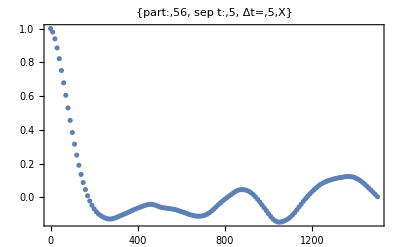

```mathematica
nombreParticula=56;separacionTemporal=5;deltaDif=5;ejeV="X"; lagDeCorrelacionFinal=300;lagDeCorrelacionIncremento=2;ListPlot[autoCorrelacionVLISTAFrames[nombreParticula,separacionTemporal,deltaDif,ejeV,{lagDeCorrelacionFinal,lagDeCorrelacionIncremento}],Frame->True,PlotRange->All,PlotLabel->{"part:",nombreParticula," sep t:",separacionTemporal," Δt=",deltaDif,ejeV}]
```

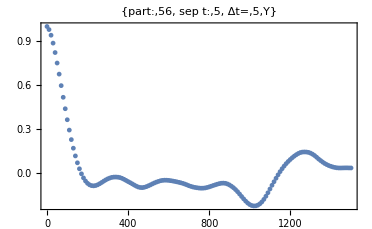

```mathematica
nombreParticula=56;separacionTemporal=5;deltaDif=5;ejeV="Y"; lagDeCorrelacionFinal=300;lagDeCorrelacionIncremento=2;ListPlot[autoCorrelacionVLISTAFrames[nombreParticula,separacionTemporal,deltaDif,ejeV,{lagDeCorrelacionFinal,lagDeCorrelacionIncremento}],Frame->True,PlotRange->All,PlotLabel->{"part:",nombreParticula," sep t:",separacionTemporal," Δt=",deltaDif,ejeV}]
```

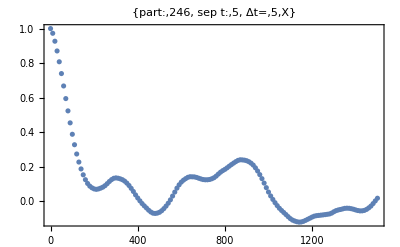

```mathematica
nombreParticula=246;separacionTemporal=5;deltaDif=5;ejeV="X"; lagDeCorrelacionFinal=300;lagDeCorrelacionIncremento=2;ListPlot[autoCorrelacionVLISTAFrames[nombreParticula,separacionTemporal,deltaDif,ejeV,{lagDeCorrelacionFinal,lagDeCorrelacionIncremento}],Frame->True,PlotRange->All,PlotLabel->{"part:",nombreParticula," sep t:",separacionTemporal," Δt=",deltaDif,ejeV}]
```

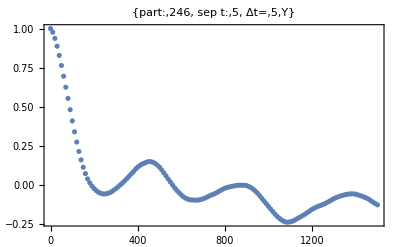

```mathematica
nombreParticula=246;separacionTemporal=5;deltaDif=5;ejeV="Y"; lagDeCorrelacionFinal=300;lagDeCorrelacionIncremento=2;ListPlot[autoCorrelacionVLISTAFrames[nombreParticula,separacionTemporal,deltaDif,ejeV,{lagDeCorrelacionFinal,lagDeCorrelacionIncremento}],Frame->True,PlotRange->All,PlotLabel->{"part:",nombreParticula," sep t:",separacionTemporal," Δt=",deltaDif,ejeV}]
```

## Autocorrelación de velocidades Vx o Vy promediada sobre partículas/series distintas

```mathematica
longitudMinimadelasSeries=20000;separacionTemporal=10;deltaDif=10;ejeV="Y"; lagDeCorrelacionFinal=100;lagDeCorrelacionIncremento=10;autoCorrelacionVPromediada[longitudMinimadelasSeries,separacionTemporal,deltaDif,ejeV,{lagDeCorrelacionFinal,lagDeCorrelacionIncremento}]
```

{{0,1.},{100,0.383856},{200,-0.055192},{300,-0.0586075},{400,-0.0184988},{500,-0.0470656},{600,-0.0435405},{700,-0.0350989},{800,-0.0291709},{900,-0.0275285},{1000,-0.0669926}}

```mathematica
longitudMinimadelasSeriesV=19000;listaParticulasconNumerodeDatosMayoroIgualque[longitudMinimadelasSeriesV]
```

{{57,20001},{56,20001},{50,20001},{7,20001},{2,20001},{52,19870}}

```mathematica
longitudMinimadelasSeries=19000;separacionTemporal=10;deltaDif=5;ejeV="X"; lagDeCorrelacionFinal=150;lagDeCorrelacionIncremento=2;autoCorrelacionVPromediada[longitudMinimadelasSeries,separacionTemporal,deltaDif,ejeV,{lagDeCorrelacionFinal,lagDeCorrelacionIncremento}]
```

{{0,1.},{20,0.932285},{40,0.813664},{60,0.673881},{80,0.52792},{100,0.3888},{120,0.266935},{140,0.164593},{160,0.0853864},{180,0.0293831},{200,-0.00585239},{220,-0.0240223},{240,-0.0295029},{260,-0.0271269},{280,-0.0203032},{300,-0.0104779},{320,-0.00218508},{340,0.0055781},{360,0.0133663},{380,0.0200824},{400,0.0237773},{420,0.0243757},{440,0.0230727},{460,0.0195078},{480,0.0140941},{500,0.00494647},{520,-0.00676296},{540,-0.0187923},{560,-0.0275199},{580,-0.0348122},{600,-0.0393534},{620,-0.0402887},{640,-0.0411821},{660,-0.0424863},{680,-0.0436187},{700,-0.0454},{720,-0.0458424},{740,-0.0439226},{760,-0.04082},{780,-0.0390117},{800,-0.0383987},{820,-0.0379953},{840,-0.0371709},{860,-0.0370354},{880,-0.0391129},{900,-0.0435721},{920,-0.0503088},{940,-0.0584169},{960,-0.0644152},{980,-0.0684219},{1000,-0.0699933},{1020,-0.0682353},{1040,-0.062271},{1060,-0.0536401},{1080,-0.0435544},{1100,-0.0338217},{1120,-0.0236679},{1140,-0.0146358},{1160,-0.00762693},{1180,-0.00252524},{1200,-0.000327},{1220,-0.00109896},{1240,-0.00211189},{1260,-0.00452664},{1280,-0.00782995},{1300,-0.0106536},{1320,-0.0135733},{1340,-0.0152521},{1360,-0.0157343},{1380,-0.016695},{1400,-0.017631},{1420,-0.0187879},{1440,-0.0194538},{1460,-0.0182938},{1480,-0.0151331},{1500,-0.0105055}}

```mathematica
longitudMinimadelasSeries=19000;separacionTemporal=10;deltaDif=5;ejeV="Y"; lagDeCorrelacionFinal=150;lagDeCorrelacionIncremento=2;autoCorrelacionVPromediada[longitudMinimadelasSeries,separacionTemporal,deltaDif,ejeV,{lagDeCorrelacionFinal,lagDeCorrelacionIncremento}]
```

{{0,1.},{20,0.934924},{40,0.813354},{60,0.665523},{80,0.509085},{100,0.36048},{120,0.229085},{140,0.122283},{160,0.04204},{180,-0.0139606},{200,-0.0487216},{220,-0.0650723},{240,-0.0669325},{260,-0.060565},{280,-0.0503511},{300,-0.0391879},{320,-0.0291463},{340,-0.0200933},{360,-0.0140677},{380,-0.0128087},{400,-0.0163454},{420,-0.023645},{440,-0.0339623},{460,-0.0439219},{480,-0.0497762},{500,-0.0519753},{520,-0.0527916},{540,-0.0517791},{560,-0.0490314},{580,-0.0448463},{600,-0.0403499},{620,-0.0369651},{640,-0.0338726},{660,-0.0309451},{680,-0.0294684},{700,-0.0292771},{720,-0.028615},{740,-0.0275225},{760,-0.0270926},{780,-0.0252093},{800,-0.0224267},{820,-0.0204313},{840,-0.0192625},{860,-0.0188248},{880,-0.0192751},{900,-0.021813},{920,-0.0265054},{940,-0.033065},{960,-0.0415932},{980,-0.0498825},{1000,-0.0567226},{1020,-0.0603675},{1040,-0.0630438},{1060,-0.0655193},{1080,-0.0667656},{1100,-0.0666811},{1120,-0.0648172},{1140,-0.0610735},{1160,-0.0554299},{1180,-0.0459683},{1200,-0.0342037},{1220,-0.0219923},{1240,-0.0114599},{1260,-0.00368748},{1280,0.000941612},{1300,0.00248212},{1320,0.00104041},{1340,-0.00472088},{1360,-0.0130549},{1380,-0.0231609},{1400,-0.0336724},{1420,-0.0447213},{1440,-0.0540759},{1460,-0.0608121},{1480,-0.0659467},{1500,-0.0674537}}

```mathematica
etiquetaAvgV[longitudMinimadelasSeries_,lagCalculoVelocidad_,deltaDif_,eje_]:="Average eje "<>eje<>" sobre series con long min="<>ToString[longitudMinimadelasSeries]<>"\n lag V="<>ToString[lagCalculoVelocidad]<>" con Δ="<>ToString[deltaDif]<>" . Unidades abcisa: frames";
```

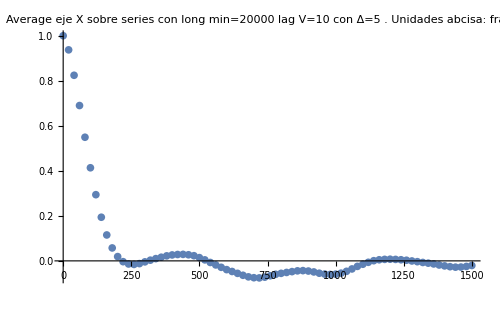

```mathematica
longitudMinimadelasSeries=20000;separacionTemporal=10;deltaDif=5;ejeV="X"; lagDeCorrelacionFinal=150;lagDeCorrelacionIncremento=2;jj=autoCorrelacionVPromediada[longitudMinimadelasSeries,separacionTemporal,deltaDif,ejeV,{lagDeCorrelacionFinal,lagDeCorrelacionIncremento}];
ListPlot[jj,PlotRange->All,PlotLabel->etiquetaAvgV[longitudMinimadelasSeries,separacionTemporal,deltaDif,ejeV]]
```

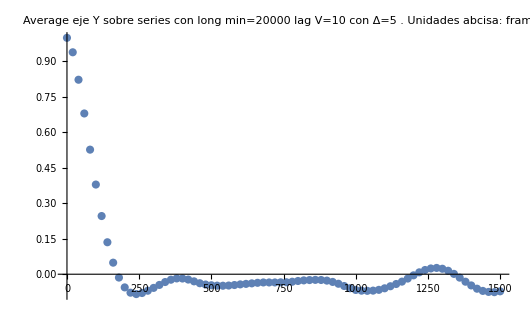

```mathematica
longitudMinimadelasSeries=20000;separacionTemporal=10;deltaDif=5;ejeV="Y"; lagDeCorrelacionFinal=150;lagDeCorrelacionIncremento=2;jj=autoCorrelacionVPromediada[longitudMinimadelasSeries,separacionTemporal,deltaDif,ejeV,{lagDeCorrelacionFinal,lagDeCorrelacionIncremento}];
ListPlot[jj,PlotRange->All,PlotLabel->etiquetaAvgV[longitudMinimadelasSeries,separacionTemporal,deltaDif,ejeV]]
```

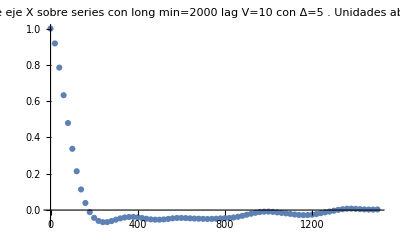

```mathematica
longitudMinimadelasSeries=2000;separacionTemporal=10;deltaDif=5;ejeV="X"; lagDeCorrelacionFinal=150;lagDeCorrelacionIncremento=2;jj=autoCorrelacionVPromediada[longitudMinimadelasSeries,separacionTemporal,deltaDif,ejeV,{lagDeCorrelacionFinal,lagDeCorrelacionIncremento}];
ListPlot[jj,PlotRange->All,PlotLabel->etiquetaAvgV[longitudMinimadelasSeries,separacionTemporal,deltaDif,ejeV]]
```

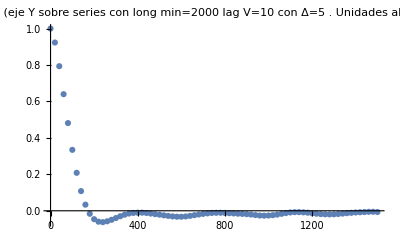

```mathematica
longitudMinimadelasSeries=2000;separacionTemporal=10;deltaDif=5;ejeV="Y"; lagDeCorrelacionFinal=150;lagDeCorrelacionIncremento=2;jj=autoCorrelacionVPromediada[longitudMinimadelasSeries,separacionTemporal,deltaDif,ejeV,{lagDeCorrelacionFinal,lagDeCorrelacionIncremento}];
ListPlot[jj,PlotRange->All,PlotLabel->etiquetaAvgV[longitudMinimadelasSeries,separacionTemporal,deltaDif,ejeV]]
```

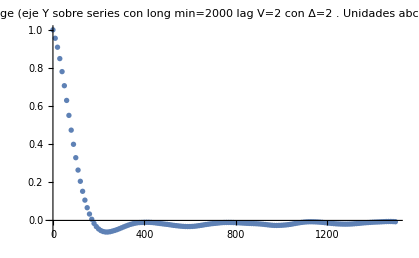

```mathematica
longitudMinimadelasSeries=2000;separacionTemporal=2;deltaDif=2;ejeV="Y"; lagDeCorrelacionFinal=750;lagDeCorrelacionIncremento=5;jj=autoCorrelacionVPromediada[longitudMinimadelasSeries,separacionTemporal,deltaDif,ejeV,{lagDeCorrelacionFinal,lagDeCorrelacionIncremento}];
ListPlot[jj,PlotRange->All,PlotLabel->etiquetaAvgV[longitudMinimadelasSeries,separacionTemporal,deltaDif,ejeV]]
```

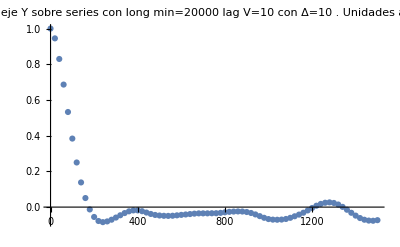

```mathematica
longitudMinimadelasSeries=20000;separacionTemporal=10;deltaDif=10;ejeV="Y"; lagDeCorrelacionFinal=150;lagDeCorrelacionIncremento=2;jj=autoCorrelacionVPromediada[longitudMinimadelasSeries,separacionTemporal,deltaDif,ejeV,{lagDeCorrelacionFinal,lagDeCorrelacionIncremento}];
ListPlot[jj,PlotRange->All,PlotLabel->etiquetaAvgV[longitudMinimadelasSeries,separacionTemporal,deltaDif,ejeV]]
```

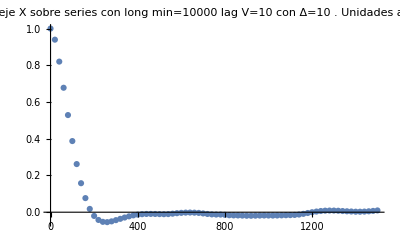

```mathematica
longitudMinimadelasSeries=10000;separacionTemporal=10;deltaDif=10;ejeV="X"; lagDeCorrelacionFinal=150;lagDeCorrelacionIncremento=2;jj=autoCorrelacionVPromediada[longitudMinimadelasSeries,separacionTemporal,deltaDif,ejeV,{lagDeCorrelacionFinal,lagDeCorrelacionIncremento}];
ListPlot[jj,PlotRange->All,PlotLabel->etiquetaAvgV[longitudMinimadelasSeries,separacionTemporal,deltaDif,ejeV]]
```

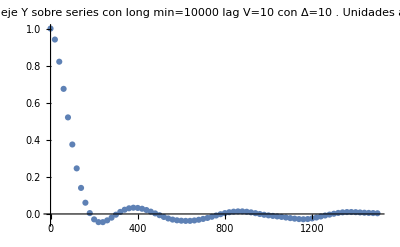

```mathematica
longitudMinimadelasSeries=10000;separacionTemporal=10;deltaDif=10;ejeV="Y"; lagDeCorrelacionFinal=150;lagDeCorrelacionIncremento=2;jj=autoCorrelacionVPromediada[longitudMinimadelasSeries,separacionTemporal,deltaDif,ejeV,{lagDeCorrelacionFinal,lagDeCorrelacionIncremento}];
ListPlot[jj,PlotRange->All,PlotLabel->etiquetaAvgV[longitudMinimadelasSeries,separacionTemporal,deltaDif,ejeV]]
```